# dirac16complex Kohn-Sham DFT in the static primordial field: symbolic 2x2 reduction, NDSolve spectra and a Wolfram Language self-consistent loop cross-checking the Rust CVODE solver

This notebook is generated by scripts/build_dirac16complex_ks_mathematica_notebook.wls and evaluated headless by scripts/verify_dirac16complex_ks_mathematica_notebook.wls. It cross-checks Stage 4 of the dirac16complex project (the 16-component complex Grassmann spinor field of Pin(4,4), treated in Kohn-Sham density-functional theory in the static primordial gravitational field) against the Rust solver studies/dirac16complex_kohn_sham, which finds every single-particle level by CVODE shooting (Pruefer angle) on the pure-Rust SUNDIALS 7.8.0 engine of rustSolveIt and iterates the Kohn-Sham equations with Anderson mixing.

What is done here, in order. (1) The exact-theory package wolfram/Dirac16ComplexKohnSham.wl is loaded and its complete check suite is run. (2) The 2x2 Kohn-Sham block equations are derived symbolically: the covariant Dirac operator of the Stage-1 geometry package in the warped y-chart, the mode ansatz, the exact block diagonalisation, the real two-component form the Rust code integrates, and the Pruefer-angle form with its boundary conditions. (3) The k = 0, lambda = 0 box problem is solved analytically (zero mode and +-sqrt(M^2 + (n pi/L)^2) for the even brane parity, tan(pL) = -p/M for the odd one). (4) The k != 0 single-particle problem is solved numerically with NDSolve shooting (bag condition at y = -L, parity condition at the brane y = 0) and compared level by level with the six free-spectrum files of the Rust spectrum/ output and its closed-shell tables. (5) A small self-consistent Kohn-Sham loop is run in Wolfram Language for N = 8, T = 0, L = 3, m = H = 1 at the coupling lambda_hat_2 of the Rust outputs, and its eigenvalues, M_eff(y), v_x(y), densities and E_0 are compared with the Rust scf/ run of the same parameters, together with the complete single-particle spectrum of the final potential. (6) The binary is run with print-config (RunProcess, SUCCESS contract) and its printed equations are compared with the derived ones. (7) Figures, the report artifacts/dirac16complex/kohn-sham/mathematica-report.json and the final association notebookChecks.

Provenance. None of the three rustSolveIt repositories contains a Mathematica notebook (recorded in Stage 3), so there is no upstream pattern to copy; this notebook follows the Stage-3 notebook notebooks/Dirac16ComplexDarkSector.nb and its builder/verifier (held Input cells, RunProcess + Import[CSV/RawJSON] exchange with the compiled binary, a fail-fast notebookChecks association).

Honesty rules. Every number shown or written to the report is computed in this notebook from the committed Rust outputs (artifacts/dirac16complex/kohn-sham/rust/spectrum and rust/scf), from the exact package, or from this notebook's own NDSolve computations; nothing is typed in by hand. Parameter values quoted in the prose are compared with the output files by a check near the end. The Wolfram and Rust computations share the discretisation conventions that define the discrete Kohn-Sham problem (the 301-point y grid, the natural cubic spline of M_eff(y) and v_x(y) between grid points, Simpson quadrature for the energy integrals, the torus spacing Delta k = 0.25 m); these are stated where they are used. They share no code: the integrator (NDSolve versus CVODE), the root finder, the mixing and the symbolic derivation are independent.

Physics summary (conventions of CONTRACT.md and STAGE4_SPEC.md sections 1-8; H = 1 units). Static primordial field in the proper hidden coordinate y = ln(sin z)/(6H) in [-L, 0]: ds^2 = dy^2 - dx4^2 + e^{2Hy}[e^{2 a4} dx_vec^2 - e^{-2 a4} dy_vec^2] (x4 = time, x5..x7 the extra times), sqrt|g| = e^{6Hy}, R = -42 H^2, so 8D Einstein gravity would need rho_req = -21 H^2/kappa and p_req = +15 H^2/kappa (STAGE4_SPEC erratum E4.3). Z2 brane at y = 0 (rho_brane = +12 H/kappa, p_brane = -10 H/kappa, verified by the package), tip cutoff at y = -L. Mode ansatz Psi = e^{-i eps x4} e^{i k x1} e^{-3Hy} chi(y); eight 2x2 blocks of two inequivalent types j = +-1 (4-fold each at fixed k), block ODE chi' = [M_eff sigma3 - kappa k sigma2 + i j (eps - v_v) sigma1] chi with kappa = e^{-Hy - a4}. Exact local exchange e_x = -(lambda/32)(n^2 + S^2), v_v = -(lambda/16) n, v_s = -(lambda/16) S, M_eff = m + (15/16) lambda S_p. The Kohn-Sham fermion-gas thermodynamics pseudo-potential is the pair (M_eff(y), v_x(y; n_p, T)) from the Mermin finite-T functional; there is no correlation term (a contact interaction beyond Hartree-Fock is not renormalisable in 8D).

## Repository, packages and committed outputs

The repository root comes from $Dirac16RepositoryRoot (set by the verifier) or from the notebook's location. Two packages are loaded: the Stage-1 geometry package (symbolic vielbein geometry, canonical spin connection Omega_mu = (1/2) omega_{mu ab} S^{ab}, Dirac operator gamma^mu D_mu) and the Stage-4 exact Kohn-Sham theory package. The Rust outputs are read from artifacts/dirac16complex/kohn-sham/rust/.

```mathematica
repositoryRoot=If[ValueQ[$Dirac16RepositoryRoot],$Dirac16RepositoryRoot,ParentDirectory[NotebookDirectory[]]];ksRoot=FileNameJoin[{repositoryRoot,"artifacts","dirac16complex","kohn-sham"}];rustRoot=FileNameJoin[{ksRoot,"rust"}];figureDirectory=FileNameJoin[{ksRoot,"figures","mathematica"}];reportPath=FileNameJoin[{ksRoot,"mathematica-report.json"}];Get[FileNameJoin[{repositoryRoot,"wolfram","Dirac16ComplexGeometry.wl"}]];Get[FileNameJoin[{repositoryRoot,"wolfram","Dirac16ComplexKohnSham.wl"}]];If[!DirectoryQ[figureDirectory],CreateDirectory[figureDirectory,CreateIntermediateDirectories->True]];spectrumSummary=Import[FileNameJoin[{rustRoot,"spectrum","summary.json"}],"RawJSON"];scfSummary=Import[FileNameJoin[{rustRoot,"scf","summary.json"}],"RawJSON"];relativePath[path_String]:=StringRiffle[Drop[FileNameSplit[ExpandFileName[path]],Length[FileNameSplit[ExpandFileName[repositoryRoot]]]],"/"];sourceFiles={};registerSource[path_String]:=(If[!MemberQ[sourceFiles,path],AppendTo[sourceFiles,path]];path);registerSource/@{FileNameJoin[{repositoryRoot,"wolfram","Dirac16ComplexGeometry.wl"}],FileNameJoin[{repositoryRoot,"wolfram","Dirac16ComplexKohnSham.wl"}],FileNameJoin[{rustRoot,"spectrum","summary.json"}],FileNameJoin[{rustRoot,"scf","summary.json"}]};Association["spectrumVerdict"->spectrumSummary["verdict"],"scfVerdict"->scfSummary["verdict"]]
```

## The exact Kohn-Sham theory package

D16KSRun[root] runs every exact check of wolfram/Dirac16ComplexKohnSham.wl (geometry and Z2 brane, reduction to eight 2x2 blocks with the explicit basis, current matrices and boundary conditions, the exact local exchange, the Mermin-Kohn-Sham functional, the energy-momentum tensor of a Kohn-Sham orbital). Its progress messages are suppressed here; the checks and measurements are kept. The zero-mode splitting coefficient c (the first-order slope d eps/dk of the k = 0 brane zero mode, exact in closed form) is taken from its measurements and used in the box section below.

```mathematica
theoryRun=Block[{Print},Dirac16ComplexKohnSham`D16KSRun[repositoryRoot]];theoryChecks=theoryRun["checks"];theoryCheckSummary=Association["checkCount"->Length[theoryChecks],"failed"->Keys[Select[theoryChecks,!TrueQ[#1]&]],"zeroModeSplittingCoefficient"->theoryRun["measurements"]["reduction_zeroModeSplittingCoefficient"]];theoryCheckSummary
```

## Symbolic derivation of the 2x2 Kohn-Sham block equations

### Geometry of the static field in the y chart

Diagonal vielbein of the warped form, coordinates (y, x1, ..., x7) with x0 = y the proper hidden coordinate and x4 the time: e = diag(1, W e^{a4} (x3), 1, W e^{-a4} (x3)), W = e^{Hy}, a4 constant (the static member of the primordial family). The Christoffel symbols and the mixed Einstein tensor are computed here independently of the packages (the same helper functions as in the Stage-3 notebook) and compared with the Stage-4 results: sqrt|g| = e^{6Hy}, G^mu_nu = H^2 diag(15,15,15,15,21,15,15,15), R = -42 H^2, hence rho_req = -G^4_4/kappa = -21 H^2/kappa and p_req = G^i_i/kappa = +15 H^2/kappa (T^mu_nu = G^mu_nu/kappa, rho = -T^4_4, p_i = T^i_i).

```mathematica
gammas=Dirac16ComplexKohnSham`D16KSGammas[];gam[a_Integer]:=gammas⟦a+1⟧;id16=IdentityMatrix[16];zero16=ConstantArray[0,{16,16}];zero2=ConstantArray[0,{2,2}];coords={yy,x1,x2,x3,x4,x5,x6,x7};warp=Exp[hH yy];kappaKS=Exp[-hH yy-a4];frameKS=DiagonalMatrix[{1,warp Exp[a4],warp Exp[a4],warp Exp[a4],1,warp Exp[-a4],warp Exp[-a4],warp Exp[-a4]}];geoKS=Dirac16Complex`Geometry`D16GeoSymbolicGeometry[frameKS,coords];metricKS=geoKS["metric"];simpKS=Simplify[#1,hH>0&&{yy,a4}∈Reals]&;christoffelOf[metric_,xs_]:=Module[{inv=metric,n=Length[xs]},Table[1/2 ∑_s^n inv⟦r,s⟧ (D[metric⟦s,m⟧, xs⟦nn⟧]+D[metric⟦s,nn⟧, xs⟦m⟧]-D[metric⟦m,nn⟧, xs⟦s⟧]),{r,n},{m,n},{nn,n}]];einsteinMixedOf[metric_,xs_,simp_]:=Module[{gc=christoffelOf[metric,xs],n=Length[xs],ricci,mixed,scalar},ricci=Table[∑_r^n (D[gc⟦r,nu,s⟧, xs⟦r⟧]-D[gc⟦r,r,s⟧, xs⟦nu⟧])+∑_r^n ∑_l^n (gc⟦r,r,l⟧ gc⟦l,nu,s⟧-gc⟦r,nu,l⟧ gc⟦l,r,s⟧),{s,n},{nu,n}];mixed=simp[metric.ricci];scalar=simp[Tr[mixed]];simp[mixed-1/2 scalar IdentityMatrix[n]]];einsteinKS=einsteinMixedOf[metricKS,coords,simpKS];ricciScalarKS=simpKS[-Tr[einsteinKS]/3];geometryChecks=Association["gammasEqualGeometryPackage"->gammas===Dirac16Complex`Geometry`D16GeoGammas,"christoffelAgreesWithPackage"->simpKS[christoffelOf[metricKS,coords]-geoKS["christoffel"]]===ConstantArray[0,{8,8,8}],"sqrtDetIsE6Hy"->simpKS[Det[metricKS]-Exp[12 hH yy]]===0&&simpKS[PowerExpand[√Det[metricKS]]-Exp[6 hH yy]]===0,"einsteinTensorIsDiag15_21"->simpKS[einsteinKS-hH^2 DiagonalMatrix[{15,15,15,15,21,15,15,15}]]===ConstantArray[0,{8,8}],"ricciScalarMinus42H2"->simpKS[ricciScalarKS+42 hH^2]===0,"requiredSourceRhoMinus21PPlus15"->simpKS[-einsteinKS⟦5,5⟧/kap+(21 hH^2)/kap]===0&&AllTrue[{1,2,3,4,6,7,8},simpKS[einsteinKS⟦#1,#1⟧/kap-(15 hH^2)/kap]===0&]];{Diagonal[einsteinKS],ricciScalarKS,geometryChecks}
```

### The reduced Dirac equation

gamma^mu D_mu Psi = M_eff Psi with the ansatz Psi = e^{-i eps x4} e^{i k x1} e^{-3Hy} chi(y) (sector without extra-time momentum, k = (k,0,0) by rotational symmetry). Dividing by the prefactor leaves A chi' + B chi = 0 with A = gamma^0 and B = i kappa k gamma^1 - i eps gamma^4 - M_eff: the factor W^{-3} = e^{-3Hy} removes the spin-connection term gamma^mu Omega_mu = 3H gamma^0 exactly (without it the term 3H gamma^0 chi remains), and the measure sqrt|g| Psi^dagger Psi = chi^dagger chi is flat in y. The Kohn-Sham equation adds the local exchange potential as the shift eps -> eps - v_v(y) and uses M_eff = m + (15/16) lambda S_p: chi' = gamma^0 [M_eff - i kappa k gamma^1 + i (eps - v_v) gamma^4] chi.

```mathematica
chiFun=Table[chiC[i][yy],{i,0,15}];chiDer=Table[chiC[i]'[yy],{i,0,15}];prefactorKS=Exp[-ⅈ eps x4+ⅈ kk x1-3 hH yy];reducedKS=Simplify[(Dirac16Complex`Geometry`D16GeoSymbolicDirac[geoKS,prefactorKS chiFun,coords]-meff[yy] prefactorKS chiFun)/prefactorKS];derivMatKS=D[reducedKS, {chiDer}];restMatKS=Simplify[D[(reducedKS/.Thread[chiDer->0]), {chiFun}]];reducedNoW=Simplify[(Dirac16Complex`Geometry`D16GeoSymbolicDirac[geoKS,Exp[-ⅈ eps x4+ⅈ kk x1] chiFun,coords])/Exp[-ⅈ eps x4+ⅈ kk x1]];odeMatrix16=gam[0].(meff[yy] id16-ⅈ kk kappaKS gam[1]+ⅈ (eps-vv[yy]) gam[4]);reductionChecks=Association["reducedEquationIsLinear"->Simplify[reducedKS-derivMatKS.chiDer-restMatKS.chiFun]===ConstantArray[0,16],"derivativeMatrixIsGamma0"->derivMatKS===gam[0],"restMatrixIsIKappaKGamma1MinusIEpsGamma4MinusM"->Simplify[restMatKS-(ⅈ kk kappaKS gam[1]-ⅈ eps gam[4]-meff[yy] id16)]===zero16,"odeFormAtZeroExchange"->Simplify[(odeMatrix16/.vv[yy]->0)+derivMatKS.restMatKS]===zero16,"withoutW3the3HGamma0TermRemains"->Simplify[reducedNoW-(gam[0].chiDer+3 hH gam[0].chiFun+ⅈ kk kappaKS gam[1].chiFun-ⅈ eps gam[4].chiFun)]===ConstantArray[0,16],"flatMeasure"->simpKS[PowerExpand[√Det[metricKS]] Exp[-6 hH yy]-1]===0];{odeMatrix16⟦1;;4,1;;4⟧,reductionChecks}
```

### Exact block diagonalisation

D16KSBlockBasis[] is the exact unitary basis of the package (columns v+, v- = gamma^0 gamma^1 v+ per block, entries in {0, +-1, +-i}/(2 sqrt 2)), the common eigenbasis of J = gamma^0 gamma^1 gamma^4, gamma^2 gamma^3 and gamma^5 gamma^6. Transforming the 16x16 ODE matrix shows that it is block diagonal with eight 2x2 blocks N_j = M_eff sigma3 - kappa k sigma2 + i j (eps - v_v) sigma1, where j = +-1 is the eigenvalue of J on the block (four blocks each): two inequivalent types, and N_{-1}(eps) = N_{+1}(2 v_v - eps), i.e. h_{-1} - v_v = -(h_{+1} - v_v). The scalar-density operator B C is j sigma2 on every block and the number-density operator is the identity.

```mathematica
blockBasis=Dirac16ComplexKohnSham`D16KSBlockBasis[];toBlocks[mat_]:=Simplify[ConjugateTranspose[blockBasis].mat.blockBasis];blockPart[mat_,b_Integer]:=mat⟦2 b-1;;2 b,2 b-1;;2 b⟧;offBlockEntries[mat_]:=Flatten[Table[If[Ceiling[r/2]≠Ceiling[c/2],mat⟦r,c⟧,Nothing],{r,16},{c,16}]];{sigma1,sigma2,sigma3}=PauliMatrix/@{1,2,3};blockFormula[j_]:=meff[yy] sigma3-kappaKS kk sigma2+ⅈ j (eps-vv[yy]) sigma1;jOperator=gam[0].gam[1].gam[4];jBlocks=toBlocks[jOperator];jEigen=Table[jBlocks⟦2 b-1,2 b-1⟧,{b,8}];odeBlocks=toBlocks[odeMatrix16];kreinB=-ⅈ Dirac16Complex`Geometry`D16GeoC.gam[4];scalarBlocks=toBlocks[kreinB.Dirac16Complex`Geometry`D16GeoC];blockChecks=Association["basisUnitary"->Simplify[ConjugateTranspose[blockBasis].blockBasis]===id16,"basisDiagonalisesJ"->jBlocks===DiagonalMatrix[Flatten[({#1,#1}&)/@jEigen]]&&Sort[jEigen]==={-1,-1,-1,-1,1,1,1,1},"odeMatrixBlockDiagonal"->AllTrue[offBlockEntries[odeBlocks],#1===0&],"blocksEqualNj"->AllTrue[Range[8],Simplify[blockPart[odeBlocks,#1]-blockFormula[jEigen⟦#1⟧]]===zero2&],"twoInequivalentTypesFourEach"->Length[Union[Table[blockPart[odeBlocks,b],{b,8}]]]===2&&Counts[jEigen]===Association[1->4,-1->4],"hMinusIsMinusHPlus"->Simplify[blockFormula[-1]-(blockFormula[1]/.eps->2 vv[yy]-eps)]===zero2,"scalarDensityOperatorIsJSigma2"->AllTrue[Range[8],blockPart[scalarBlocks,#1]===jEigen⟦#1⟧ sigma2&]&&AllTrue[offBlockEntries[scalarBlocks],#1===0&]];{MatrixForm/@{blockFormula[1],blockFormula[-1]},blockChecks}
```

### The real two-component form integrated by the Rust code

With chi = (a, i b) and a, b real, the block ODE of type j becomes the real system a' = M_eff a + (s (eps - v_v) - kappa k) b, b' = -(s (eps - v_v) + kappa k) a - M_eff b with s = -j. This is the form printed by the binary (print-config line reduction, below) and implemented in studies/dirac16complex_kohn_sham/src/shooting.rs. The next cell derives it and reads the Rust block basis compiled into src/generated.rs: its eight blocks carry the labels (s, c1, c2) of BLOCK_LABELS, and applying the basis to the 16x16 ODE matrix reproduces the block formula with j = -s. Measured labelling fact (recorded in the report): on every Rust block the eigenvalue of J = gamma^0 gamma^1 gamma^4 is -s, i.e. s is the eigenvalue of gamma^1 gamma^0 gamma^4 = -J, while the comment in generated.rs reads J = s. Both block types enter every sum over states with the same multiplicity, so the label convention does not change any result. The scalar density of an orbital is chi^dagger (j sigma2) chi = -2 s a b and the number density a^2 + b^2, the formulas of scf.rs.

```mathematica
realPair={aR[yy],ⅈ bR[yy]};realFormFromBlock[j_]:=Module[{rhs=blockFormula[j].realPair},Simplify[{rhs⟦1⟧,-ⅈ rhs⟦2⟧}]];rustRealForm[s_]:={meff[yy] aR[yy]+(s (eps-vv[yy])-kappaKS kk) bR[yy],-(s (eps-vv[yy])+kappaKS kk) aR[yy]-meff[yy] bR[yy]};generatedKS=Import[FileNameJoin[{repositoryRoot,"studies","dirac16complex_kohn_sham","src","generated.rs"}],"Text"];registerSource[FileNameJoin[{repositoryRoot,"studies","dirac16complex_kohn_sham","src","generated.rs"}]];rustConstantKS[name_String]:=Module[{start,tail,stop},start=StringPosition[generatedKS,"pub const "<>name<>":"]⟦1,2⟧;tail=StringDrop[generatedKS,start];stop=StringPosition[tail,"pub const "];If[stop=!={},tail=StringTake[tail,stop⟦1,1⟧-1]];ToExpression/@StringCases[tail,RegularExpression["-?[0-9]+\\.[0-9]+"]]];rustGammaValuesKS=rustConstantKS["GAMMA"];rustBlockLabels=ToExpression[StringReplace[First[StringCases[generatedKS,"BLOCK_LABELS: [[i32; 3]; BLOCK_COUNT] = "~~x:Shortest[__]~~";":>x]],{"["->"{","]"->"}"}]];rustBasisRe=ArrayReshape[Round[rustConstantKS["BLOCK_BASIS_RE"]],{8,2,16}];rustBasisIm=ArrayReshape[Round[rustConstantKS["BLOCK_BASIS_IM"]],{8,2,16}];rustBasis=Transpose[Flatten[rustBasisRe+ⅈ rustBasisIm,1]]/(√32);rustJ=Simplify[ConjugateTranspose[rustBasis].jOperator.rustBasis];rustC1=Simplify[ConjugateTranspose[rustBasis].(ⅈ gam[2].gam[3]).rustBasis];rustOdeBlocks=Simplify[ConjugateTranspose[rustBasis].odeMatrix16.rustBasis];fixturePath=FileNameJoin[{repositoryRoot,"artifacts","dirac16complex","arbitrary-field","algebra-fixture.json"}];fixtureHash=ToLowerCase[FileHash[fixturePath,"SHA256",All,"HexString"]];registerSource[fixturePath];realFormChecks=Association["realFormIsBlockODEWithSMinusJ"->AllTrue[{1,-1},Simplify[realFormFromBlock[#1]-rustRealForm[-#1]]==={0,0}&]&&Simplify[realFormFromBlock[1]-rustRealForm[1]]=!={0,0},"sMinusOneIsMirrorOfSPlusOne"->Simplify[rustRealForm[-1]-(rustRealForm[1]/.{eps->-eps,vv[yy]->-vv[yy]})]==={0,0},"scalarDensityIsMinus2sab"->AllTrue[{1,-1},Simplify[ComplexExpand[Conjugate[realPair].(#1 sigma2).realPair]--2 (-#1) aR[yy] bR[yy]]===0&],"numberDensityIsA2PlusB2"->Simplify[ComplexExpand[Conjugate[realPair].realPair]-(aR[yy]^2+bR[yy]^2)]===0,"rustGammasEqualPackage"->Length[rustGammaValuesKS]==8 16 16&&ArrayReshape[Round[rustGammaValuesKS],{8,16,16}]===gammas&&Max[Abs[rustGammaValuesKS-Round[rustGammaValuesKS]]]==0,"rustFixtureHashIsFixture"->First[StringCases[generatedKS,"FIXTURE_SHA256: &str = \""~~h:(HexadecimalCharacter..)~~"\"":>ToLowerCase[h]]]===fixtureHash,"rustBasisUnitary"->Simplify[ConjugateTranspose[rustBasis].rustBasis]===id16,"rustBasisBlockDiagonalisesWithJMinusS"->AllTrue[offBlockEntries[rustOdeBlocks],#1===0&]&&AllTrue[Range[8],Simplify[blockPart[rustOdeBlocks,#1]-blockFormula[-rustBlockLabels⟦#1,1⟧]]===zero2&],"rustLabelSIsMinusJEigenvalue"->rustJ===DiagonalMatrix[Flatten[({-#1,-#1}&)/@rustBlockLabels⟦All,1⟧]],"rustLabelC1IsIGamma2Gamma3"->rustC1===DiagonalMatrix[Flatten[({#1,#1}&)/@rustBlockLabels⟦All,2⟧]]];{realFormFromBlock[-1],rustBlockLabels,realFormChecks}
```

### Pruefer angle, boundary conditions and the y-current

Writing a = r cos(theta), b = -r sin(theta) turns the real system into theta' = s (eps - v_v) + kappa k cos(2 theta) - M_eff sin(2 theta) (derived below by solving for theta' and r'). Boundary conditions (STAGE4_SPEC E4.5 in block form): tip bag chi_2(-L) = 0, i.e. b(-L) = 0, i.e. theta(-L) = 0; brane parity + chi_2(0) = 0, i.e. b(0) = 0, i.e. theta(0) = n pi; brane parity - chi_1(0) = 0, i.e. a(0) = 0, i.e. theta(0) = pi/2 + n pi. The variational equation of theta with respect to eps has the solution d theta(0)/d eps = s Integral exp(...) dy, so Theta(eps) := theta(0; eps) is strictly monotone (increasing for s = +1, decreasing for s = -1): every level in an energy window corresponds to exactly one integer n between Theta at the window edges (oscillation count), and n is the Pruefer index of the Rust output. The y-current chi^dagger (j sigma1) chi = 2 j Re(chi_1^* chi_2) vanishes when chi_1 = 0 or chi_2 = 0, i.e. at the brane for either parity and at the tip for the bag; a real standing wave chi = (a, i b) carries no current anywhere.

```mathematica
pruferSystem={aP'[yy]-(meff[yy] aP[yy]+(s (eps-vv[yy])-kappaKS kk) bP[yy]),bP'[yy]-(-(s (eps-vv[yy])+kappaKS kk) aP[yy]-meff[yy] bP[yy])};polarRules={aP->Function[t,rP[t] Cos[thP[t]]],bP->Function[t,-rP[t] Sin[thP[t]]]};pruferSolved=First[Solve[Thread[(pruferSystem/.polarRules)==0],{thP'[yy],rP'[yy]}]];thetaRHS=Simplify[thP'[yy]/.pruferSolved];variationalCoefficient=D[thetaRHS, thP[yy]];dThetaCandidate[t_]:=s Exp[gG[t]] ∫_-lL^t Exp[-gG[u]]ⅆu;currentOf[chi_]:=Conjugate[chi].(jj sigma1).chi;complexChi={c1+ⅈ d1,c2+ⅈ d2};pruferChecks=Association["pruferEquation"->Simplify[TrigReduce[thetaRHS-(s (eps-vv[yy])+kappaKS kk Cos[2 thP[yy]]-meff[yy] Sin[2 thP[yy]])]]===0,"variationalCoefficient"->Simplify[TrigReduce[variationalCoefficient-(-2 kappaKS kk Sin[2 thP[yy]]-2 meff[yy] Cos[2 thP[yy]])]]===0,"pruferMonotoneInEps"->Simplify[D[dThetaCandidate[yy], yy]-(s+gG'[yy] dThetaCandidate[yy])]===0&&dThetaCandidate[-lL]===0,"bagIsThetaZero"->(-rP[yy] Sin[thP[yy]]/.thP[yy]->0)===0,"parityPlusTargetsNPi"->Sort[t/.Solve[Sin[t]==0&&-10<t<10,t]]===Sort[π Range[-3,3]],"parityMinusTargetsHalfPiPlusNPi"->Sort[t/.Solve[Cos[t]==0&&-10<t<10,t]]===Sort[π/2+π Range[-3,2]],"currentVanishesForEitherComponentZero"->Simplify[ComplexExpand[currentOf[complexChi]]-2 jj (c1 c2+d1 d2)]===0&&Simplify[ComplexExpand[currentOf[complexChi]]/.{c2->0,d2->0}]===0&&Simplify[ComplexExpand[currentOf[complexChi]]/.{c1->0,d1->0}]===0,"standingWaveCarriesNoCurrent"->Simplify[ComplexExpand[currentOf[realPair]]]===0];{thetaRHS,pruferChecks}
```

## The k = 0, lambda = 0 box problem: exact solution

At k = 0 and lambda = 0 (M_eff = M constant, v_v = 0) the real system of block type s is a' = M a + s eps b, b' = -s eps a - M b on [-L, 0]. Eliminating b gives a'' = -(eps^2 - M^2) a, so with p = sqrt(eps^2 - M^2) and the tip bag b(-L) = 0 (equivalently a'(-L) = M a(-L)) the solution is a = cos(p(y+L)) + (M/p) sin(p(y+L)), b = -(s eps/p) sin(p(y+L)). Brane parity +: b(0) = 0, i.e. sin(pL) = 0, p = n pi/L, eps = +-sqrt(M^2 + (n pi/L)^2), n = 1, 2, ...; brane parity -: a(0) = 0, i.e. p cos(pL) + M sin(pL) = 0, i.e. tan(pL) = -p/M, one root p_j in ((j - 1/2) pi/L, j pi/L) for j = 1, 2, .... Below threshold (|eps| < M, p = i q) the brane values are a(0) = cosh(qL) + (M/q) sinh(qL) > 0 (no parity - level) and b(0) = -(s eps/q) sinh(qL), which vanishes only at eps = 0: there q = M and the solution is the brane zero mode a = e^{M(y+L)}, b = 0 (parity +, normalisable even for L -> infinity, localised at the brane). At the threshold eps = +-M neither condition holds. Level labels (the Pruefer index n of the Rust output, Theta = n pi or pi/2 + n pi): parity +, s = +1: eps = sign(n) sqrt(M^2 + (n pi/L)^2), n = 0 the zero mode; parity -, s = +1: n >= 0 gives +sqrt(M^2 + p_(n+1)^2), n < 0 gives -sqrt(M^2 + p_(-n)^2); the s = -1 levels are eps_(-1)(n) = -eps_(+1)(n) (the s = -1 system is the s = +1 system at -eps).

```mathematica
boxA[y_]:=Cos[pB (y+lB)]+(mB Sin[pB (y+lB)])/pB;boxB[y_]:=-((sB eB) Sin[pB (y+lB)])/pB;boxODE[a_,b_,e_]:={D[a, yy]-(mB a+sB e b),D[b, yy]-(-sB e a-mB b)};boxAssume=mB>0&&pB>0&&lB>0&&qB>0&&yy∈Reals;boxChecks=Association["boxSolutionSolvesODE"->AllTrue[Tuples[{{1,-1},{1,-1}}],Simplify[boxODE[boxA[yy],boxB[yy],eB]/.{sB->#1⟦1⟧,eB->#1⟦2⟧ √(mB^2+pB^2)},boxAssume]==={0,0}&],"boxSolutionSatisfiesTipBag"->Simplify[boxB[-lB]]===0&&Simplify[(D[boxA[yy], yy]/.yy->-lB)-mB boxA[-lB]]===0,"parityPlusIsSinPL"->Simplify[boxB[0]+((sB eB) Sin[pB lB])/pB]===0&&Simplify[boxB[0]/.pB->(nB π)/lB,nB∈Integers&&lB>0]===0,"parityMinusIsTanPLMinusPOverM"->Simplify[pB boxA[0]-(pB Cos[pB lB]+mB Sin[pB lB])]===0,"parityMinusBracketSignChange"->Simplify[(mB Sin[pB lB]+pB Cos[pB lB]/.pB->((jB-1/2) π)/lB)-mB (-1)^(jB+1),jB∈Integers]===0&&Simplify[(mB Sin[pB lB]+pB Cos[pB lB]/.pB->(jB π)/lB)-(jB π (-1)^jB)/lB,jB∈Integers]===0,"zeroModeSolvesODEBothTypes"->AllTrue[{1,-1},Simplify[boxODE[Exp[mB yy],0,0]/.sB->#1]==={0,0}&],"zeroModeNormalisableOnHalfLine"->Integrate[Exp[2 mB yy],{yy,-∞,0},Assumptions->mB>0]===1/(2 mB),"belowThresholdParityPlusOnlyAtEpsZero"->Simplify[ComplexExpand[boxB[0]/.pB->ⅈ qB]+((sB eB) Sinh[qB lB])/qB]===0,"belowThresholdNoParityMinusLevel"->Simplify[ComplexExpand[boxA[0]/.pB->ⅈ qB]-(Cosh[qB lB]+(mB Sinh[qB lB])/qB)]===0&&Simplify[Cosh[qB lB]+(mB Sinh[qB lB])/qB>0,boxAssume],"belowThresholdAtEpsZeroIsZeroMode"->Simplify[TrigToExp[ComplexExpand[{boxA[yy],boxB[yy]}/.pB->ⅈ qB]/.{eB->0,qB->mB}]-{Exp[mB (yy+lB)],0}]==={0,0},"thresholdIsNoLevel"->lim_(pB->0) {boxA[0],boxB[0]}==={1+mB lB,-sB eB lB}];boxChecks
```

Zero-mode splitting. By first-order perturbation theory (Hellmann-Feynman) the k = 0 zero mode chi = (e^{My}, 0) of block type j = -s moves as eps = j c k + O(k^2) with c = Integral kappa |chi|^2 / Integral |chi|^2 = Integral_{-L}^0 e^{-Hy - a4} e^{2My} dy / Integral_{-L}^0 e^{2My} dy, because the k-derivative of the block Hamiltonian h_j is j kappa sigma3 and sigma3 = +1 on (1, 0). The integral is done here, c is written in the manifestly positive product form e^{-a4} (2M/(2M - H)) (1 - e^{-(2M - H)L})/(1 - e^{-2ML}) (every factor positive for 2M > H) and compared with the closed form measured by the exact package (reduction_zeroModeSplittingCoefficient); the numerical slope is checked in the shooting section.

```mathematica
splitAssume=mB>0&&hH>0&&lB>0&&2 mB>hH&&a4∈Reals;cSplitting=Simplify[Integrate[Exp[-hH yy-a4] Exp[2 mB yy],{yy,-lB,0},Assumptions->splitAssume]/Integrate[Exp[2 mB yy],{yy,-lB,0},Assumptions->splitAssume],splitAssume];packageSplittingRaw=theoryRun["measurements"]["reduction_zeroModeSplittingCoefficient"];packageSplitting=Module[{expr=If[StringQ[packageSplittingRaw],Block[{$Context="KSPackageImport`",$ContextPath={"System`"}},ToExpression[packageSplittingRaw]],packageSplittingRaw],names=Association["LL"->lB,"H"->hH,"M"->mB,"a4c"->a4]},expr/.sym_Symbol/;Context[sym]=!="System`"&&KeyExistsQ[names,SymbolName[sym]]:>names[SymbolName[sym]]];cSplittingM1L3=cSplitting/.{mB->1,hH->1,lB->3,a4->0};splittingChecks=Association["splittingEqualsPackageClosedForm"->Simplify[cSplitting-packageSplitting,splitAssume]===0,"splittingAtM1H1L3Is2Over1PlusExpMinus3"->Simplify[cSplittingM1L3-2/(1+Exp[-3])]===0,"splittingPositiveProductForm"->Simplify[cSplitting-(Exp[-a4] (2 mB) (1-Exp[-xB]))/((2 mB-hH) (1-Exp[-2 mB lB]))/.xB->(2 mB-hH) lB,splitAssume]===0&&Simplify[(2 mB-hH) lB>0,splitAssume]&&Simplify[1-Exp[-xB]>0,xB>0]&&Simplify[(2 mB)/(2 mB-hH)>0&&1-Exp[-2 mB lB]>0,splitAssume]];{cSplitting,N[cSplittingM1L3,12],splittingChecks}
```

Comparison with the Rust free spectra. For each of the six files spectrum/free-spectrum-m{1,3}-L{2,3,4}.csv (window -4m <= eps <= 4m, shells n2 <= 16) the k = 0 rows (n2 = 0, both parities, both block types) are compared with the exact levels above, level by level through the Pruefer index. The roots p_j of the parity - condition are computed by bisection in exact arithmetic on the bracket ((j - 1/2) pi/L, j pi/L), whose end values of M sin(pL) + p cos(pL) have opposite signs (checked above), to 30 significant digits.

```mathematica
readTable[path_String]:=Module[{data=Import[registerSource[path],"CSV"]},Association["header"->First[data],"index"->AssociationThread[First[data]->Range[Length[First[data]]]],"rows"->Rest[data]]];columnOf[table_,name_String]:=table["rows"]⟦All,table["index"][name]⟧;freeConfigurations={{1,2},{1,3},{1,4},{3,2},{3,3},{3,4}};freeFileName[{mv_,lv_}]:="free-spectrum-m"<>ToString[mv]<>"-L"<>ToString[lv]<>".csv";freeTables=AssociationMap[readTable[FileNameJoin[{rustRoot,"spectrum",freeFileName[#1]}]]&,freeConfigurations];oddBoxMomentum[mv_,lv_,j_]:=oddBoxMomentum[mv,lv,j]=Module[{g,a=((j-1/2) π)/lv,b=(j π)/lv,ga,c},g[p_]:=N[mv Sin[p lv]+p Cos[p lv],40];ga=Sign[g[a]];Do[c=(a+b)/2;If[Sign[g[c]]==ga,a=c,b=c],{110}];N[(a+b)/2,30]];analyticBoxLevel[mv_,lv_,parity_,s_,n_]:=s If[parity==1,If[n==0,0,Sign[n] √(mv^2+((n π)/lv)^2)],If[n≥0,√(mv^2+oddBoxMomentum[mv,lv,n+1]^2),-√(mv^2+oddBoxMomentum[mv,lv,-n]^2)]];analyticBoxLevels[mv_,lv_]:=Module[{plusMax=Floor[(lv √15 mv)/π],minusMax=1},While[√(mv^2+oddBoxMomentum[mv,lv,minusMax+1]^2)<4 mv,minusMax++];Select[Flatten[Table[Join[Table[Association["parity"->1,"s"->s,"index"->n,"eps"->N[analyticBoxLevel[mv,lv,1,s,n],30]],{n,-plusMax,plusMax}],Table[Association["parity"->-1,"s"->s,"index"->n,"eps"->N[analyticBoxLevel[mv,lv,-1,s,n],30]],{n,-minusMax,minusMax-1}]],{s,{1,-1}}]],Abs[#1["eps"]]<4 mv&]];rustRowsK0[config_]:=Module[{t=freeTables[config]},Select[t["rows"],#1⟦t["index"]["n2"]⟧==0&]];keyOf[r_]:=Lookup[r,{"parity","s","index"}];boxComparison=Association[Table[Module[{t=freeTables[config],exact,rust,dev},exact=SortBy[analyticBoxLevels@@config,keyOf];rust=SortBy[(Association["parity"->Round[#1⟦t["index"]["parity"]⟧],"s"->Round[#1⟦t["index"]["s"]⟧],"index"->Round[#1⟦t["index"]["index"]⟧],"eps"->#1⟦t["index"]["eps"]⟧]&)/@rustRowsK0[config],keyOf];dev=If[keyOf/@exact===keyOf/@rust,Max[Abs[rust⟦All,"eps"⟧-N[exact⟦All,"eps"⟧]]],∞];freeFileName[config]->Association["levels"->Length[exact],"rustLevels"->Length[rust],"keysIdentical"->keyOf/@exact===keyOf/@rust,"maxAbsDeviation"->dev]],{config,freeConfigurations}]];boxLevelsExact=AssociationMap[analyticBoxLevels@@#1&,freeConfigurations];Dataset[boxComparison]
```

## NDSolve shooting for the k != 0 single-particle problem

The eigenvalue problem of one block type s at momentum k is solved by NDSolve shooting with the Pruefer angle derived above: theta' = s (eps - v_v(y)) + kappa(y) k cos(2 theta) - M_eff(y) sin(2 theta), theta(-L) = 0 (the tip bag b(-L) = 0), integrated to the brane; the level condition is Theta(eps) := theta(0; eps) = n pi (brane parity +, b(0) = 0) or pi/2 + n pi (parity -, a(0) = 0). Because Theta is strictly monotone in eps (increasing for s = +1, decreasing for s = -1), the integers n between Theta at the two window edges enumerate every level in the window exactly once (oscillation count: no level is missed), and n is the Pruefer index of the Rust output. The variational equation theta_eps' = s + (-2 kappa k sin(2 theta) - 2 M_eff cos(2 theta)) theta_eps, theta_eps(-L) = 0 (its coefficient was derived symbolically above), is integrated together with theta and gives the exact derivative dTheta/deps. The integration runs in u = y + L in [0, L], so that NDSolve never has to land on the endpoint y = 0 (landing there produced step-size warnings in a trial). ParametricNDSolveValue returns (Theta, dTheta/deps) as a function of (eps, k, s). For a constant potential NDSolve runs with its automatic method (non-stiff/stiff switching) at PrecisionGoal 13, AccuracyGoal 14; for the spline potentials of the self-consistent loop, whose third derivative jumps at each of the 301 nodes, the automatic method needed about 4600 steps per integration in a trial, and the explicit Runge-Kutta method of order 5 is used instead at PrecisionGoal 12, AccuracyGoal 13 (about 700 steps, Theta error about 1e-12 against a WorkingPrecision 24 reference in the same trial). Level search in a group (k, s, parity): Theta at the two window edges gives the targets; Theta is sampled at n_levels + 1 further equally spaced energies (a group without levels costs two integrations); each root of Theta(eps) - target is found by Newton's method with the exact derivative, started at the linear interpolation inside the sample cell that brackets the target and safeguarded by that bracket (a step that leaves it is replaced by bisection), and stopped at the first Newton step below 1e-10 max(1, |eps|), which is taken (clipped to the bracket) (the error after such a step is of the order of its square, below the integration error). At every root the linear two-component system (a(-L) = 1, b(-L) = 0, with the accumulators Integral(a^2 + b^2), Integral(-2ab) and Integral(-kappa k (a^2 - b^2))) is integrated separately; it gives the matching residual |b(0)|/|chi(0)| (parity +) or |a(0)|/|chi(0)| (parity -) and the charges of the state of block type s, the scalar charge Integral(-2 s a b)/Integral(a^2 + b^2) (the scalar density of type s is -2 s a b, derived above) and the 3-space pressure charge Integral(-s kappa k (a^2 - b^2))/Integral(a^2 + b^2), i.e. the columns scalar_charge and pressure_charge of the Rust files. Both codes shoot on the same Pruefer form; they share no code: NDSolve versus CVODE, Newton with the variational derivative versus bracketing plus Illinois regula falsi in Rust, and the symbolic derivation of the Pruefer equation above.

```mathematica
smoothOptions={PrecisionGoal->13,AccuracyGoal->14};splineOptions={Method->{"ExplicitRungeKutta","DifferenceOrder"->5},PrecisionGoal->12,AccuracyGoal->13};pruferThetaD[mF_,vF_,lv_,hv_,av_,opts_List]:=ParametricNDSolveValue[{thS'[uS]==sS (epsS-vF[uS-lv])+Exp[-hv (uS-lv)-av] kS Cos[2 thS[uS]]-mF[uS-lv] Sin[2 thS[uS]],teS'[uS]==sS+(-2 Exp[-hv (uS-lv)-av] kS Sin[2 thS[uS]]-2 mF[uS-lv] Cos[2 thS[uS]]) teS[uS],thS[0]==0,teS[0]==0},{thS[lv],teS[lv]},{uS,0,lv},{epsS,kS,sS},Sequence@@opts,MaxSteps->∞];linearEnds[mF_,vF_,lv_,hv_,av_,opts_List]:=ParametricNDSolveValue[{aS'[uS]==mF[uS-lv] aS[uS]+(sS (epsS-vF[uS-lv])-Exp[-hv (uS-lv)-av] kS) bS[uS],bS'[uS]==-(sS (epsS-vF[uS-lv])+Exp[-hv (uS-lv)-av] kS) aS[uS]-mF[uS-lv] bS[uS],nS'[uS]==aS[uS]^2+bS[uS]^2,qS'[uS]==-2 aS[uS] bS[uS],pS'[uS]==-Exp[-hv (uS-lv)-av] kS (aS[uS]^2-bS[uS]^2),aS[0]==1,bS[0]==0,nS[0]==0,qS[0]==0,pS[0]==0},{aS[lv],bS[lv],nS[lv],qS[lv],pS[lv]},{uS,0,lv},{epsS,kS,sS},Sequence@@opts,MaxSteps->∞];newtonRoot[g_,{a0_,b0_},{fa0_,fb0_},x0_]:=Module[{a=N[a0],b=N[b0],fa=fa0,x=N[x0],f,d,xn,iterations=0},If[fa0==0.,Return[{a,0}]];If[fb0==0.,Return[{b,0}]];While[iterations<60,iterations++;{f,d}=g[x];If[f==0.,Break[]];If[f fa<0,b=x,a=x;fa=f];xn=x-f/d;If[Abs[xn-x]≤Max[1,Abs[x]]/10^10,x=Clip[xn,{Min[a,b],Max[a,b]}];Break[]];If[!Min[a,b]<xn<Max[a,b],xn=(a+b)/2];x=xn];{x,iterations}];rootInBracket[theta_,k_,s_,target_,{lo_,hi_},x0_]:=Module[{flo=First[theta[N[lo],k,s]]-target,fhi=First[theta[N[hi],k,s]]-target},If[flo fhi>0,{$Failed,60},newtonRoot[theta[#1,k,s]-{target,0}&,{lo,hi},{flo,fhi},x0]]];groupLevels[theta_,ends_,k_,s_,parity_,{lo_,hi_}]:=Module[{tlo,thi,off=If[parity==1,0,π/2],ns,es,vals},tlo=First[theta[N[lo],k,s]];thi=First[theta[N[hi],k,s]];ns=Range[Ceiling[(Min[tlo,thi]-off)/π],Floor[(Max[tlo,thi]-off)/π]];If[ns==={},Return[{}]];es=N[Subdivide[lo,hi,Length[ns]+1]];vals=Join[{tlo},(First[theta[#1,k,s]]&)/@es⟦2;;-2⟧,{thi}];Table[Module[{target=N[off+n π],cell,x0,root,e},cell=SelectFirst[Range[Length[es]-1],(vals⟦#1⟧-target) (vals⟦#1+1⟧-target)≤0&];x0=es⟦cell⟧+((target-vals⟦cell⟧) (es⟦cell+1⟧-es⟦cell⟧))/(vals⟦cell+1⟧-vals⟦cell⟧);root=newtonRoot[theta[#1,k,s]-{target,0}&,es⟦{cell,cell+1}⟧,vals⟦{cell,cell+1}⟧-target,x0];e=ends[root⟦1⟧,k,s];Association["parity"->parity,"s"->s,"index"->n,"eps"->root⟦1⟧,"iterations"->root⟦2⟧,"matching"->If[parity==1,Abs[e⟦2⟧],Abs[e⟦1⟧]]/(√(e⟦1⟧^2+e⟦2⟧^2)),"scalarCharge"->(s e⟦4⟧)/e⟦3⟧,"pressureCharge"->(s e⟦5⟧)/e⟦3⟧]],{n,ns}]];shellLevels[theta_,ends_,k_,window_]:=Join@@Flatten[Table[groupLevels[theta,ends,k,s,parity,window],{parity,{1,-1}},{s,{1,-1}}],1];freePotential[mv_]:={Evaluate[N[mv]]&,0.&};representableShells[max_]:=Select[Range[0,max],SquaresR[3,#1]>0&];fullKey[r_]:=Lookup[r,{"n2","parity","s","index"}];toolTest=Module[{theta=pruferThetaD[1.&,0.&,3.,1.,0.,smoothOptions],ends=linearEnds[1.&,0.&,3.,1.,0.,smoothOptions],lev,fd},lev=groupLevels[theta,ends,0.,1,1,{-2.,2.}];fd=(First[theta[0.7+1/10^5,0.5,1]]-First[theta[0.7-1/10^5,0.5,1]])/(2/10^5);Association["levels"->lev⟦All,"index"⟧,"maxDeviationFromExactBox"->Max[Abs[lev⟦All,"eps"⟧-N[(analyticBoxLevel[1,3,1,1,#1]&)/@lev⟦All,"index"⟧]]],"variationalDerivativeVsCentralDifference"->Abs[Last[theta[0.7,0.5,1]]-fd]/Abs[fd]]];toolTest
```

Zero-mode splitting, numerically: the parity +, index 0 level of each block type at small k (m = H = 1, L = 3, a4 = 0) gives the slope d eps/dk at k = 0 by Richardson extrapolation, (4 eps(h) - eps(2h))/(2h) = d eps/dk + O(h^2), h = 1e-4 (tolerance 1e-6 for the O(h^2) truncation; the eigenvalue error of about 1e-13 contributes about 1e-9). The exact slope is -s c (j = -s).

```mathematica
zeroModeSlope=Module[{theta=pruferThetaD[1.&,0.&,3.,1.,0.,smoothOptions],h=1/10^4,level},level[k_,s_]:=First[rootInBracket[theta,N[k],s,0.,{-0.2,0.2},0.]];Association[Table[s->(4 level[h,s]-level[2 h,s])/(2 h),{s,{1,-1}}]]];zeroModeSlopeDeviation=Max[Abs[zeroModeSlope[1]+N[cSplittingM1L3]],Abs[zeroModeSlope[-1]-N[cSplittingM1L3]]];{zeroModeSlope,N[cSplittingM1L3],zeroModeSlopeDeviation}
```

The six Rust free-spectrum files are recomputed completely: every representable shell n2 <= 16 (lattice multiplicity g(n2) = SquaresR[3, n2], the number of integer vectors with n1^2 + n2^2 + n3^2 = n2), both parities, both block types, every level in -4m <= eps <= 4m, with k = 0.25 m sqrt(n2) (torus spacing Delta k = 0.25 m). The two lists are matched by the key (n2, parity, s, Pruefer index); a missing or extra level makes the key lists differ. Compared: eps, the k and multiplicity (4 g) columns, scalar_charge and pressure_charge; the k = 0 levels are also compared with the exact box levels. Tolerances: 1e-8 for eigenvalues and scalar charges (the acceptance threshold of the Rust code's own analytic box check, free_box_spectrum_analytic) and 1e-8 relative to max(1, |charge|) for the pressure charges, whose magnitude grows with k; the linear-system matching residuals must stay below 1e-8.

```mathematica
freeSpectrumRun[config_]:=Module[{mv,lv,t,idx,mF,vF,theta,ends,dk,mine={},rust,keysOK,matched},{mv,lv}=config;t=freeTables[config];idx=t["index"];{mF,vF}=freePotential[mv];theta=pruferThetaD[mF,vF,N[lv],1.,0.,smoothOptions];ends=linearEnds[mF,vF,N[lv],1.,0.,smoothOptions];dk=0.25 mv;Do[With[{k=dk √N[n2]},mine=Join[mine,(Join[#1,Association["n2"->n2,"k"->k,"multiplicity"->4 SquaresR[3,n2]]]&)/@shellLevels[theta,ends,k,{-4. mv,4. mv}]]],{n2,representableShells[16]}];rust=(Association["n2"->Round[#1⟦idx["n2"]⟧],"parity"->Round[#1⟦idx["parity"]⟧],"s"->Round[#1⟦idx["s"]⟧],"index"->Round[#1⟦idx["index"]⟧],"eps"->#1⟦idx["eps"]⟧,"k"->#1⟦idx["k"]⟧,"multiplicity"->#1⟦idx["multiplicity"]⟧,"scalarCharge"->#1⟦idx["scalar_charge"]⟧,"pressureCharge"->#1⟦idx["pressure_charge"]⟧]&)/@t["rows"];mine=SortBy[mine,fullKey];rust=SortBy[rust,fullKey];keysOK=fullKey/@mine===fullKey/@rust;matched=If[keysOK,Transpose[{mine,rust}],{}];Association["levels"->Length[mine],"rustLevels"->Length[rust],"keysIdentical"->keysOK,"maxAbsDeviation"->If[keysOK,Max[(Abs[#1⟦1,"eps"⟧-#1⟦2,"eps"⟧]&)/@matched],∞],"maxScalarChargeDeviation"->If[keysOK,Max[(Abs[#1⟦1,"scalarCharge"⟧-#1⟦2,"scalarCharge"⟧]&)/@matched],∞],"maxPressureChargeDeviation"->If[keysOK,Max[(Abs[#1⟦1,"pressureCharge"⟧-#1⟦2,"pressureCharge"⟧]&)/@matched],∞],"maxPressureChargeRelativeDeviation"->If[keysOK,Max[(Abs[#1⟦1,"pressureCharge"⟧-#1⟦2,"pressureCharge"⟧]/Max[1,Abs[#1⟦2,"pressureCharge"⟧]]&)/@matched],∞],"kColumnMaxDeviation"->If[keysOK,Max[(Abs[#1⟦1,"k"⟧-#1⟦2,"k"⟧]&)/@matched],∞],"multiplicityColumnIdentical"->keysOK&&AllTrue[matched,#1⟦1,"multiplicity"⟧==#1⟦2,"multiplicity"⟧&],"k0VsExactBoxMaxAbsDeviation"->Module[{k0=SortBy[Select[mine,#1["n2"]==0&],keyOf],exact=SortBy[boxLevelsExact[config],keyOf]},If[keyOf/@k0===keyOf/@exact,Max[Abs[k0⟦All,"eps"⟧-N[exact⟦All,"eps"⟧]]],∞]],"maxMatchingResidual"->Max[mine⟦All,"matching"⟧],"maxRootIterations"->Max[mine⟦All,"iterations"⟧],"mine"->mine]];freeSpectrumResults=AssociationMap[freeSpectrumRun,freeConfigurations];Dataset[KeyMap[freeFileName,(KeyDrop[#1,"mine"]&)/@freeSpectrumResults]]
```

Error attribution. At the level with the largest notebook-Rust deviation of each of the six files, Theta is recomputed with NDSolve at WorkingPrecision 32 (PrecisionGoal 24, AccuracyGoal 26; the ODE has exact coefficients, the momentum is the machine k of the discrete problem), and one Newton step from the notebook's eigenvalue with a central-difference derivative (step 1e-8) gives a reference eigenvalue whose error is far below 1e-12 (the Newton error is of the order of the square of the notebook's error). The deviations of the notebook's and of the Rust eigenvalue from this reference show which side carries the difference.

```mathematica
errorAttributionOf[config_]:=Module[{mv,lv,res=freeSpectrumResults[config],t=freeTables[config],idx,rust,worst,target,k,e0,th,f0,d,ref},{mv,lv}=config;idx=t["index"];rust=Association[(Round/@#1⟦{idx["n2"],idx["parity"],idx["s"],idx["index"]}⟧->#1⟦idx["eps"]⟧&)/@t["rows"]];worst=First[MaximalBy[res["mine"],Abs[#1["eps"]-rust[fullKey[#1]]]&]];target=If[worst["parity"]==1,0,π/2]+worst["index"] π;k=SetPrecision[worst["k"],40];e0=SetPrecision[worst["eps"],40];th[e_]:=NDSolveValue[{thH'[uH]==worst["s"] e+Exp[-(uH-lv)] k Cos[2 thH[uH]]-mv Sin[2 thH[uH]],thH[0]==0},thH[lv],{uH,0,lv},WorkingPrecision->32,PrecisionGoal->24,AccuracyGoal->26,MaxSteps->∞];f0=th[e0]-target;d=(th[e0+1/10^8]-th[e0-1/10^8])/(2/10^8);ref=e0-f0/d;Association["key"->fullKey[worst],"k"->worst["k"],"referenceEps"->N[ref],"notebookMinusReference"->N[worst["eps"]-ref],"rustMinusReference"->N[rust[fullKey[worst]]-ref]]];errorAttribution=Association[(freeFileName[#1]->errorAttributionOf[#1]&)/@freeConfigurations];Dataset[errorAttribution]
```

Closed shells. The Rust study picks its particle numbers from the closed shells of the free spectrum at L = 3 (spectrum/summary.json: closedShells_m1_L3_N_epsHomo and closedShells_m3_L3_N_epsHomo, also written as closed-shells-m{1,3}-L3.csv): the particle states (eps >= 0) sorted by eps, grouped into degenerate levels (|eps_j - eps_i| <= 1e-9 max(1, |eps_i|)), with the cumulative multiplicity 4 g(n2) recorded after each group until it exceeds 1300. Here the particle states are those with s (target - Theta(0)) >= 0 (equivalent to eps >= 0 by the monotonicity of Theta; exact for the k = 0 zero mode, where Theta(0) = 0 identically), computed in the window [-0.5 m, 1.7 m] over the shells n2 = 0, 1, 2, ... until two consecutive shells have no level in the window (the stopping rule of the Rust code). The table is complete when its last energy lies inside the window and its count exceeds 1300; that no shell beyond the stop has a level in the window is the stopping-rule assumption (the lowest |eps| of a shell grows with k), supported here by the measured increase of the lowest particle level with n2. N_mid and N_large are the closed-shell numbers (N > 8) nearest 100 and 1000.

```mathematica
closedShellRun[mv_]:=Module[{mF,vF,theta,ends,window={-0.5 mv,1.7 mv},states={},empty=0,used=0,particles,total=0,table={},i=1,lowest},{mF,vF}=freePotential[mv];theta=pruferThetaD[mF,vF,3.,1.,0.,smoothOptions];ends=linearEnds[mF,vF,3.,1.,0.,smoothOptions];Do[Module[{k=0.25 mv √N[n2],lev},lev=shellLevels[theta,ends,k,window];lev=(Join[#1,Association["n2"->n2,"k"->k,"multiplicity"->4 SquaresR[3,n2],"particle"->#1["s"] (N[If[#1["parity"]==1,0,π/2]+#1["index"] π]-First[theta[0.,k,#1["s"]]])≥0]]&)/@lev;used++;If[lev==={},empty++,empty=0];states=Join[states,lev];If[empty≥2,Break[]]],{n2,representableShells[5000]}];particles=SortBy[Select[states,#1["particle"]&],#1["eps"]&];While[i≤Length[particles],Module[{e=particles⟦i,"eps"⟧,j=i},While[j≤Length[particles]&&Abs[particles⟦j,"eps"⟧-e]≤Max[1,Abs[e]]/10^9,total+=particles⟦j,"multiplicity"⟧;j++];AppendTo[table,{total,e}];If[total>1300,Break[]];i=j]];lowest=Min/@Values[GroupBy[Select[states,#1["particle"]&&#1["n2"]>0&],#1["n2"]&,#1⟦All,"eps"⟧&]];Association["table"->table,"shellsUsed"->used,"statesInWindow"->Length[states],"complete"->table=!={}&&table⟦-1,1⟧>1300&&table⟦-1,2⟧<window⟦2⟧,"lowestParticleLevelIncreasesWithN2"->OrderedQ[lowest],"branchMatchesEpsSign"->AllTrue[states,#1["particle"]==(#1["eps"]≥-1/10^12)&],"nearest"->Function[target,First[MinimalBy[Select[table,#1⟦1⟧>8&],Abs[#1⟦1⟧-target]&]]⟦1⟧]]];closedShellResults=AssociationMap[closedShellRun,{1,3}];rustClosedShells=Association[1->spectrumSummary["reference"]["closedShells_m1_L3_N_epsHomo"],3->spectrumSummary["reference"]["closedShells_m3_L3_N_epsHomo"]];rustClosedShellCSV=AssociationMap[Module[{t=readTable[FileNameJoin[{rustRoot,"spectrum","closed-shells-m"<>ToString[#1]<>"-L3.csv"}]]},Transpose[{columnOf[t,"N"],columnOf[t,"eps_homo"]}]]&,{1,3}];closedShellComparison=Association[Table[mv->Module[{mine=closedShellResults[mv]["table"],rust=rustClosedShells[mv]},Association["entries"->Length[mine],"rustEntries"->Length[rust],"countsIdentical"->Length[mine]==Length[rust]&&mine⟦All,1⟧==rust⟦All,1⟧,"maxAbsDeviation"->If[Length[mine]==Length[rust],Max[Abs[mine⟦All,2⟧-rust⟦All,2⟧]],∞],"csvEqualsSummary"->rustClosedShellCSV[mv]==N[rust],"shellsUsed"->closedShellResults[mv]["shellsUsed"],"complete"->closedShellResults[mv]["complete"],"lowestParticleLevelIncreasesWithN2"->closedShellResults[mv]["lowestParticleLevelIncreasesWithN2"],"branchMatchesEpsSign"->closedShellResults[mv]["branchMatchesEpsSign"]]],{mv,{1,3}}]];closedShellNumbers=Association["nMid"->closedShellResults[1]["nearest"][100],"nLarge"->closedShellResults[1]["nearest"][1000],"nMidM3"->closedShellResults[3]["nearest"][100]];{Dataset[closedShellComparison],closedShellNumbers,N[Lookup[spectrumSummary["reference"],{"nMid","nLarge","nMidM3"}]]}
```

```mathematica
shootingResult=Association["toolTestMaxDeviationFromExactBox"->toolTest["maxDeviationFromExactBox"],"variationalDerivativeRelativeDeviation"->toolTest["variationalDerivativeVsCentralDifference"],"zeroModeSplittingC_m1_L3"->N[cSplittingM1L3],"zeroModeSlopes"->KeyMap[ToString,zeroModeSlope],"zeroModeSlopeMaxDeviation"->zeroModeSlopeDeviation,"boxExactVsRust"->KeyMap[ToString,boxComparison],"freeSpectra"->Association[KeyValueMap[freeFileName[#1]->KeyDrop[#2,"mine"]&,freeSpectrumResults]],"closedShells"->KeyMap["m"<>ToString[#1]<>"_L3"&,closedShellComparison],"closedShellNumbers"->closedShellNumbers,"errorAttribution"->errorAttribution];shootingChecks=Association["boxExactLevelsEqualRustK0"->AllTrue[Values[boxComparison],#1["keysIdentical"]&&#1["maxAbsDeviation"]≤1/10^8&],"shootingToolReproducesExactBox"->toolTest["maxDeviationFromExactBox"]≤1/10^10&&toolTest["variationalDerivativeVsCentralDifference"]≤1/10^6,"zeroModeSlopeEqualsMinusSC"->zeroModeSlopeDeviation≤1/10^6,"freeSpectraSameLevelKeys"->AllTrue[Values[freeSpectrumResults],#1["keysIdentical"]&&#1["levels"]==#1["rustLevels"]&],"freeSpectraEigenvalues"->AllTrue[Values[freeSpectrumResults],#1["maxAbsDeviation"]≤1/10^8&],"freeSpectraCharges"->AllTrue[Values[freeSpectrumResults],#1["maxScalarChargeDeviation"]≤1/10^8&&#1["maxPressureChargeRelativeDeviation"]≤1/10^8&],"freeSpectraKAndMultiplicityColumns"->AllTrue[Values[freeSpectrumResults],#1["kColumnMaxDeviation"]≤1/10^14&&#1["multiplicityColumnIdentical"]&],"freeSpectraK0NDSolveEqualsExactBox"->AllTrue[Values[freeSpectrumResults],#1["k0VsExactBoxMaxAbsDeviation"]≤1/10^10&],"freeSpectraLinearMatchingResiduals"->AllTrue[Values[freeSpectrumResults],#1["maxMatchingResidual"]≤1/10^8&&#1["maxRootIterations"]<60&],"notebookEigenvaluesWithin1e11OfHighPrecisionReference"->AllTrue[Values[errorAttribution],Abs[#1["notebookMinusReference"]]≤1/10^11&],"closedShellTablesEqualRust"->AllTrue[Values[closedShellComparison],#1["countsIdentical"]&&#1["maxAbsDeviation"]≤1/10^8&&#1["csvEqualsSummary"]&&#1["complete"]&&#1["branchMatchesEpsSign"]&],"closedShellStoppingRuleSupported"->AllTrue[Values[closedShellComparison],#1["lowestParticleLevelIncreasesWithN2"]&],"closedShellNumbersEqualRust"->Values[closedShellNumbers]==Round[Lookup[spectrumSummary["reference"],{"nMid","nLarge","nMidM3"}]]];shootingChecks
```

## A self-consistent Kohn-Sham loop in Wolfram Language (N = 8, lambda_hat_2, T = 0, L = 3, m = H = 1)

Parameter set: the Rust run scf/m1_L3_N8_lamp2_T0 (N = 8 particles, T = 0, L = 3, m = H = 1, a4 = 0, torus spacing Delta k = 0.25 m, i.e. l = 2 pi/(0.25 m), and the coupling lambda_hat_2 of the configuration (m, L, N) = (1, 3, 8) listed in spectrum/summary.json, the larger of the two couplings of the study, with lambda = lambda_hat/m^6). The discrete Kohn-Sham problem is the one the Rust code defines: the potentials M_eff(y) = m + (15/16) lambda S_p(y) and v_x(y) = v_v(y) = -(lambda/16) n_p(y) are tabulated on the uniform 301-point grid of [-L, 0] and interpolated by the natural cubic spline (spline.rs; here an Interpolation of the node values and the spline's node derivatives with InterpolationOrder 3, a piecewise cubic Hermite interpolant, which is the natural spline itself because a cubic is fixed by its end values and derivatives; checked below against the explicit spline formula), clamped to the grid; the proper densities are n_p = e^{-6Hy} n_c and S_p = e^{-6Hy} S_c with the coordinate densities n_c = Sum mult w (a^2 + b^2)/l^3 and S_c = Sum mult w (-2 s a b)/l^3 of the normalised orbitals on the grid; the energy E = Sum mult w eps - Integral[(lambda/2) S_p^2 + e_x] dV_p with dV_p = e^{6Hy} l^3 dy and e_x = -(lambda/32)(n_p^2 + S_p^2) uses the composite Simpson rule on the grid (shooting.rs: simpson). These are the definitions of the discrete problem; the computation itself (NDSolve, root search, mixing) is independent. Scope: this notebook compares one self-consistent parameter set; the other Rust runs are cross-checked by the independent Python reference solver (scripts/ks_reference_solver.py, scripts/check_dirac16complex_kohn_sham.py), not here.

```mathematica
scfLabel="m1_L3_N8_lamp2_T0";scfRecord=SelectFirst[scfSummary["runs"],#1["label"]===scfLabel&];scfDirectory=FileNameJoin[{rustRoot,"scf",scfLabel}];scfRun=Import[registerSource[FileNameJoin[{scfDirectory,"run.json"}]],"RawJSON"];scfProfiles=readTable[FileNameJoin[{scfDirectory,"profiles.csv"}]];scfLevelsTable=readTable[FileNameJoin[{scfDirectory,"levels.csv"}]];scfHistory=readTable[FileNameJoin[{scfDirectory,"history.csv"}]];coupling8=SelectFirst[spectrumSummary["reference"]["couplings"],#1["N"]==8&&#1["m"]==1&&#1["L"]==3&];{scfMass,scfLength,scfH,scfA4,scfGridN,scfDk,scfLambdaHat,scfLambda,scfN,scfTol}=N[Lookup[scfRun["parameters"],{"m","L","H","a4_0","gridPoints","deltaKOverM","lambdaHat","lambda","N","tol"}]];scfGridN=Round[scfGridN];scfGrid=Table[If[i==scfGridN-1,0.,-scfLength+(scfLength i)/(scfGridN-1.)],{i,0,scfGridN-1}];scfDy=scfLength/(scfGridN-1.);scfEll=(2. π)/(scfDk scfMass);scfVolume=scfEll^3;scfDensityFactor=Exp[-6. scfH scfGrid];naturalSplineSecond[values_List]:=Module[{n=Length[values]},Join[{0.},LinearSolve[SparseArray[{Band[{1,1}]->4.,Band[{1,2}]->1.,Band[{2,1}]->1.},{n-2,n-2}],(6. (values⟦3;;All⟧-2 values⟦2;;-2⟧+values⟦1;;-3⟧))/scfDy^2],{0.}]];naturalSpline[values_List]:=Module[{n=Length[values],sec=naturalSplineSecond[values],der,f},der=Append[Table[(values⟦i+1⟧-values⟦i⟧)/scfDy-1/6 scfDy (2 sec⟦i⟧+sec⟦i+1⟧),{i,n-1}],(values⟦n⟧-values⟦n-1⟧)/scfDy+1/6 scfDy (sec⟦n-1⟧+2 sec⟦n⟧)];f=Interpolation[Transpose[{List/@scfGrid,values,der}],InterpolationOrder->3];Function[y,f[Clip[y,{-scfLength,0.}]]]];splineExplicit[values_List,sec_List,y_]:=Module[{i=Clip[Floor[(y+scfLength)/scfDy],{0,Length[values]-2}],a,b},a=(-scfLength+(i+1) scfDy-y)/scfDy;b=1-a;a values⟦i+1⟧+b values⟦i+2⟧+1/6 ((a^3-a) sec⟦i+1⟧+(b^3-b) sec⟦i+2⟧) scfDy^2];simpsonRule[f_List]:=Module[{n=Length[f],total=0.,i=1},While[i+2≤n,total+=1/3 scfDy (f⟦i⟧+4 f⟦i+1⟧+f⟦i+2⟧);i+=2];If[i+1≤n,total+=1/2 scfDy (f⟦i⟧+f⟦i+1⟧)];total];splineTest=Module[{values=Sin[3 scfGrid] Exp[scfGrid],f,sec,probes=N[Range[-scfLength+0.0037,-0.0011,0.0173]]},f=naturalSpline[values];sec=naturalSplineSecond[values];Association["nodes"->Max[Abs[f/@scfGrid-values]],"offNodes"->Max[Abs[f/@probes-(splineExplicit[values,sec,#1]&)/@probes]],"probes"->Length[probes]]];scfSetupChecks=Association["runIsLambdaHat2OfN8"->scfRecord=!=Missing["NotFound"]&&scfRun["parameters"]["lambdaHat"]==coupling8["lambdaHat2"]&&scfRun["parameters"]["lambda"]==coupling8["lambdaHat2"]/scfMass^6,"runParametersAsStated"->{scfMass,scfLength,scfH,scfA4,scfDk,scfN}=={1.,3.,1.,0.,0.25,8.}&&scfGridN==301&&scfRun["parameters"]["T"]==0&&scfRun["parameters"]["occupationSmearing"]==0&&TrueQ[scfRun["exactZeroTemperatureOccupations"]]&&TrueQ[scfRun["converged"]],"gridEqualsProfilesY"->Max[Abs[scfGrid-columnOf[scfProfiles,"y"]]]≤1/10^15,"torusLengthEqualsRun"->Abs[scfEll-scfRun["parameters"]["ell"]]≤scfEll/10^12,"volumeFactorEqualsProfiles"->Max[Abs[1/scfDensityFactor-columnOf[scfProfiles,"volume_factor"]]/(1/scfDensityFactor)]≤1/10^14,"hermiteInterpolantIsNaturalSpline"->splineTest["nodes"]≤1/10^14&&splineTest["offNodes"]≤1/10^13,"simpsonExactForCubics"->Abs[simpsonRule[scfGrid^3-2 scfGrid^2+1]-(scfLength-(2 scfLength^3)/3-scfLength^4/4)]≤1/10^12];{splineTest,scfSetupChecks}
```

The loop. Occupations: at T = 0 the aufbau fills the N = 8 lowest particle-branch states; in this run these are the k = 0, parity +, index 0 levels of the two block types (4 states each: the four blocks of each type; lattice multiplicity 1), the continuation of the brane zero modes. The loop therefore solves only these two levels in each iteration (Newton on Theta bracketed by the energy window of the Rust run and started at the eigenvalue of the previous iteration, 0 in the first); that they are the eight lowest particle states of the final potential, with a gap to the next one, is verified afterwards from the complete spectrum in the window (next cells). One iteration: potentials from the input densities (spline) -> the two levels by Pruefer shooting -> their normalised profiles (linear system, NDSolve with the spline options above, normalised by the accumulated Integral(a^2 + b^2)) sampled on the grid -> output densities. Mixing: Anderson (Pulay) on the pair (n_c, S_c) with beta = 0.4 and a history of 6 (the values of the Rust run; a different mixing converges to the same fixed point), starting from zero densities (the free potential). Convergence: max|Delta n_c|/D and max|Delta S_c|/D below 1e-12 with D = max(max|n_c|, max|S_c|), the Rust residual definition with a tolerance 100 times smaller than the Rust run's 1e-10, so that the fixed point of this loop is determined more tightly than the one it is compared with.

```mathematica
scfPotential[dens_]:={naturalSpline[scfMass+15/16 scfLambda scfDensityFactor dens⟦2⟧],naturalSpline[1/16 (-scfLambda) scfDensityFactor dens⟦1⟧]};profileOnGrid[pot_,k_,s_,eps_]:=Module[{mF=pot⟦1⟧,vF=pot⟦2⟧,sol,norm,us=scfGrid+scfLength,a0,b0},sol=NDSolveValue[{aS'[uS]==mF[uS-scfLength] aS[uS]+(s (eps-vF[uS-scfLength])-Exp[-scfH (uS-scfLength)-scfA4] k) bS[uS],bS'[uS]==-(s (eps-vF[uS-scfLength])+Exp[-scfH (uS-scfLength)-scfA4] k) aS[uS]-mF[uS-scfLength] bS[uS],nS'[uS]==aS[uS]^2+bS[uS]^2,aS[0]==1,bS[0]==0,nS[0]==0},{aS,bS,nS},{uS,0,scfLength},Sequence@@splineOptions,MaxSteps->∞,InterpolationOrder->All];norm=sol⟦3⟧[scfLength];{a0,b0}={sol⟦1⟧[scfLength],sol⟦2⟧[scfLength]};Association["a"->(sol⟦1⟧/@us)/(√norm),"b"->(sol⟦2⟧/@us)/(√norm),"matching"->Abs[b0]/(√(a0^2+b0^2))]];scfWindow=N[{scfRun["windowLo"],scfRun["windowHi"]}];scfOutput[dens_,start_List]:=Module[{pot=scfPotential[dens],theta,roots,profiles,nc,sc},theta=pruferThetaD[pot⟦1⟧,pot⟦2⟧,scfLength,scfH,scfA4,splineOptions];roots=MapThread[rootInBracket[theta,0.,#1,0.,scfWindow,#2]&,{{1,-1},start}];profiles=MapThread[profileOnGrid[pot,0.,#1,#2]&,{{1,-1},roots⟦All,1⟧}];nc=(∑_j^2 4. ((profiles⟦j⟧["a"])^2+(profiles⟦j⟧["b"])^2))/scfVolume;sc=(∑_j^2 4. (-2 {1,-1}⟦j⟧ profiles⟦j⟧["a"] profiles⟦j⟧["b"]))/scfVolume;Association["eps"->roots⟦All,1⟧,"rootIterations"->roots⟦All,2⟧,"profiles"->profiles,"densities"->{nc,sc},"potential"->pot]];andersonStep[history_,x_,r_,beta_]:=If[Length[history]<2,x+beta r,Module[{dX=Differences[history⟦All,1⟧],dF=Differences[history⟦All,2⟧],g},g=LeastSquares[Transpose[dF],r];x+beta r-Transpose[(dX+beta dF)].g]];scfInput={ConstantArray[0.,scfGridN],ConstantArray[0.,scfGridN]};scfMixHistory={};scfResiduals={};scfConverged=False;scfStart={0.,0.};scfRootIterations={};Do[Module[{out=scfOutput[scfInput,scfStart],x=Flatten[scfInput],r,scale,resN,resS},scfStart=out["eps"];scfRootIterations=Join[scfRootIterations,out["rootIterations"]];r=Flatten[out["densities"]]-x;scale=Max[Max[Abs[out["densities"]⟦1⟧]],Max[Abs[out["densities"]⟦2⟧]]];resN=Max[Abs[out["densities"]⟦1⟧-scfInput⟦1⟧]]/scale;resS=Max[Abs[out["densities"]⟦2⟧-scfInput⟦2⟧]]/scale;AppendTo[scfResiduals,{iteration,resN,resS}];If[resN<1/10^12&&resS<1/10^12,scfConverged=True;Break[]];scfMixHistory=Take[Append[scfMixHistory,{x,r}],-Min[Length[scfMixHistory]+1,7]];scfInput=Partition[andersonStep[scfMixHistory,x,r,0.4],scfGridN]],{iteration,0,80}];scfFinal=scfOutput[scfInput,scfStart];{scfConverged,Length[scfResiduals],scfResiduals⟦-1⟧,scfFinal["eps"]}
```

Comparison with the Rust run (run.json, profiles.csv). The potentials are compared on the grid with a tolerance set by the convergence criterion of the two loops: both stop when the coordinate densities change by less than tol D (Rust tol = 1e-10), which the factor e^{6HL} of the proper densities amplifies at the tip, so the admissible difference of M_eff is 10 (15/16) |lambda| e^{6HL} tol D and that of v_x is 10 (|lambda|/16) e^{6HL} tol D (factor 10 as margin). Densities are compared relative to D (the residual scale of the loops). Eigenvalues and energies are compared absolutely with 1e-9. The Rust HOMO profile (homo_a, homo_b) is the orbital of the first state of the degenerate highest occupied group in the Rust ordering; the two block types are degenerate at k = 0 with profiles (a, b) and (a, -b) (the s = -1 equation at k = 0 is the s = +1 equation with b -> -b), so it is compared with both and the matching type is reported.

```mathematica
scfPot=scfFinal["potential"];scfMeff=scfPot⟦1⟧/@scfGrid;scfVx=scfPot⟦2⟧/@scfGrid;{scfNc,scfSc}=scfFinal["densities"];scfNp=scfDensityFactor scfNc;scfSp=scfDensityFactor scfSc;scfScale=Max[Max[Abs[scfNc]],Max[Abs[scfSc]]];scfKsSum=4. Total[scfFinal["eps"]];scfHartree=simpsonRule[(scfLambda scfSp^2 scfVolume)/(2 scfDensityFactor)];scfExchange=simpsonRule[-(scfLambda (scfNp^2+scfSp^2) scfVolume)/(32 scfDensityFactor)];scfEnergy=scfKsSum-scfHartree-scfExchange;scfLs=(scfLambda scfSp^2)/2-1/32 scfLambda (scfNp^2+scfSp^2);potentialBoundM=10/16 15 Abs[scfLambda] Exp[6 scfH scfLength] scfTol scfScale;potentialBoundV=10/16 Abs[scfLambda] Exp[6 scfH scfLength] scfTol scfScale;homoDistance[j_]:=Max[Abs[scfFinal["profiles"]⟦j⟧["a"]-columnOf[scfProfiles,"homo_a"]],Abs[scfFinal["profiles"]⟦j⟧["b"]-columnOf[scfProfiles,"homo_b"]]];scfComparison=Association["iterations"->Length[scfResiduals],"finalResidualN"->scfResiduals⟦-1,2⟧,"finalResidualS"->scfResiduals⟦-1,3⟧,"rustIterations"->scfRun["iterations"],"rustFinalResidualN"->scfRun["finalResidualN"],"rustFinalResidualS"->scfRun["finalResidualS"],"epsHomo"->First[scfFinal["eps"]],"rustEpsHomo"->scfRun["epsHomo"],"epsHomoDeviation"->Max[Abs[scfFinal["eps"]-scfRun["epsHomo"]]],"muDeviation"->Max[Abs[scfFinal["eps"]-scfRun["mu"]]],"blockTypeSplitting"->Abs[scfFinal["eps"]⟦1⟧-scfFinal["eps"]⟦2⟧],"energy"->scfEnergy,"rustEnergy"->scfRun["energy"],"energyDeviation"->Abs[scfEnergy-scfRun["energy"]],"ksSumDeviation"->Abs[scfKsSum-scfRun["ksSum"]],"hartreeDeviation"->Abs[scfHartree-scfRun["hartreeEnergy"]],"exchangeDeviation"->Abs[scfExchange-scfRun["exchangeEnergy"]],"freeEnergyDeviation"->Abs[scfEnergy-scfRun["freeEnergy"]],"grandPotentialDeviation"->Abs[scfEnergy-scfN First[scfFinal["eps"]]-scfRun["grandPotential"]],"nFromDensityDeviation"->Abs[scfVolume simpsonRule[scfNc]-scfRun["nFromDensity"]],"mEffMaxAbsDeviation"->Max[Abs[scfMeff-columnOf[scfProfiles,"M_eff"]]],"mEffTolerance"->potentialBoundM,"vxMaxAbsDeviation"->Max[Abs[scfVx-columnOf[scfProfiles,"v_x"]]],"vxTolerance"->potentialBoundV,"mEffMinusMRange"->{Min[scfMeff-scfMass],Max[scfMeff-scfMass]},"vxRange"->{Min[scfVx],Max[scfVx]},"ncMaxDeviationOverD"->Max[Abs[scfNc-columnOf[scfProfiles,"n_c"]]]/scfScale,"scMaxDeviationOverD"->Max[Abs[scfSc-columnOf[scfProfiles,"S_c"]]]/scfScale,"npMaxRelativeDeviation"->Max[Abs[scfNp-columnOf[scfProfiles,"n_p"]]]/Max[Abs[scfNp]],"spMaxRelativeDeviation"->Max[Abs[scfSp-columnOf[scfProfiles,"S_p"]]]/Max[Abs[scfSp]],"lsMaxRelativeDeviation"->Max[Abs[scfLs-columnOf[scfProfiles,"L_s"]]]/Max[Abs[scfLs]],"maxLambdaSOverMDeviation"->Abs[Max[Abs[scfLambda scfSp]]/scfMass-scfRun["maxLambdaSOverM"]],"maxVxOverMDeviation"->Abs[Max[Abs[scfVx]]/scfMass-scfRun["maxVxOverM"]],"homoProfileBlockType"->If[homoDistance[2]≤homoDistance[1],-1,1],"homoProfileMaxDeviation"->Min[homoDistance[1],homoDistance[2]],"homoTypesRelatedByBSignFlip"->Max[Abs[scfFinal["profiles"]⟦1⟧["a"]-scfFinal["profiles"]⟦2⟧["a"]],Abs[scfFinal["profiles"]⟦1⟧["b"]+scfFinal["profiles"]⟦2⟧["b"]]],"maxProfileMatchingResidual"->Max[(#1["matching"]&)/@scfFinal["profiles"]]];Dataset[scfComparison]
```

The complete spectrum of the final potential. All levels in the energy window of the Rust run (run.json windowLo, windowHi) are computed for every shell n2 = 0, 1, 2, ... (both parities, both block types; the s = -1 levels directly from the s = -1 equation with the vector potential) until two consecutive shells have no level in the window (the Rust stopping rule), and compared with levels.csv key by key. Branches (normal ordering with respect to the free Dirac sea): a state is a particle state when its free partner, the level with the same (shell, parity, s, Pruefer index) at lambda = 0, has eps_free >= 0, i.e. s (target - Theta_free(0)) >= 0 by the monotonicity of the free Theta; the eps_free column is compared for the shells n2 <= 16 with the free spectrum computed above. The aufbau of N = 8 on the particle states of this spectrum must give back the two occupied levels of the loop, and the lowest unoccupied particle level (LUMO), the KS gap and the highest sea level are compared with run.json.

```mathematica
scfFinalTheta=pruferThetaD[scfPot⟦1⟧,scfPot⟦2⟧,scfLength,scfH,scfA4,splineOptions];scfFinalEnds=linearEnds[scfPot⟦1⟧,scfPot⟦2⟧,scfLength,scfH,scfA4,splineOptions];scfFreeTheta=pruferThetaD[Evaluate[scfMass]&,0.&,scfLength,scfH,scfA4,smoothOptions];scfSpectrum=Module[{states={},empty=0,used=0},Do[Module[{k=scfDk scfMass √N[n2],lev},lev=shellLevels[scfFinalTheta,scfFinalEnds,k,scfWindow];lev=(Join[#1,Association["n2"->n2,"k"->k,"multiplicity"->4 SquaresR[3,n2],"branch"->If[#1["s"] (N[If[#1["parity"]==1,0,π/2]+#1["index"] π]-First[scfFreeTheta[0.,k,#1["s"]]])≥0,1,-1]]]&)/@lev;used++;If[lev==={},empty++,empty=0];states=Join[states,lev];If[empty≥2,Break[]]],{n2,representableShells[5000]}];Association["states"->states,"shellsUsed"->used]];scfRustLevels=Module[{t=scfLevelsTable,idx=scfLevelsTable["index"]},(Association["n2"->Round[#1⟦idx["n2"]⟧],"parity"->Round[#1⟦idx["parity"]⟧],"s"->Round[#1⟦idx["s"]⟧],"index"->Round[#1⟦idx["index"]⟧],"eps"->#1⟦idx["eps"]⟧,"branch"->Round[#1⟦idx["branch"]⟧],"epsFree"->#1⟦idx["eps_free"]⟧,"weight"->#1⟦idx["weight"]⟧,"multiplicity"->#1⟦idx["multiplicity"]⟧]&)/@t["rows"]];scfSpectrumComparison=Module[{mine=SortBy[scfSpectrum["states"],fullKey],rust=SortBy[scfRustLevels,fullKey],keysOK,pairs,freeLookup,freeDev,particles,groups,homoGroup,lumo,seaTop},keysOK=fullKey/@mine===fullKey/@rust;pairs=If[keysOK,Transpose[{mine,rust}],{}];freeLookup=Association[(fullKey[#1]->#1["eps"]&)/@freeSpectrumResults[{1,3}]["mine"]];freeDev=Max[(Abs[Lookup[freeLookup,Key[fullKey[#1⟦1⟧]]]-#1⟦2,"epsFree"⟧]&)/@Select[pairs,KeyExistsQ[freeLookup,fullKey[#1⟦1⟧]]&]];particles=SortBy[Select[mine,#1["branch"]==1&],#1["eps"]&];groups=Split[particles,Abs[#2["eps"]-#1["eps"]]≤Max[1,Abs[#1["eps"]]]/10^9&];homoGroup=First[groups];lumo=groups⟦2,1,"eps"⟧;seaTop=Max[Select[mine,#1["branch"]==-1&]⟦All,"eps"⟧];Association["levels"->Length[mine],"rustLevels"->Length[rust],"rustStatesRecord"->scfRun["states"],"keysIdentical"->keysOK,"shellsUsed"->scfSpectrum["shellsUsed"],"rustShellsUsed"->scfRun["shellsUsed"],"maxAbsDeviation"->If[keysOK,Max[(Abs[#1⟦1,"eps"⟧-#1⟦2,"eps"⟧]&)/@pairs],∞],"branchesIdentical"->keysOK&&AllTrue[pairs,#1⟦1,"branch"⟧==#1⟦2,"branch"⟧&],"epsFreeComparedStates"->Count[pairs,p_/;KeyExistsQ[freeLookup,fullKey[p⟦1⟧]]],"epsFreeMaxAbsDeviation"->freeDev,"multiplicitiesIdentical"->keysOK&&AllTrue[pairs,#1⟦1,"multiplicity"⟧==#1⟦2,"multiplicity"⟧&],"aufbauGroupCount"->Total[homoGroup⟦All,"multiplicity"⟧],"aufbauGroupKeys"->Sort[fullKey/@homoGroup],"aufbauGroupIsLoopOccupation"->Sort[fullKey/@homoGroup]==={{0,1,-1,0},{0,1,1,0}}&&Total[homoGroup⟦All,"multiplicity"⟧]==scfN,"rustOccupiedKeys"->Sort[fullKey/@Select[rust,#1["weight"]>0&]],"aufbauHomoDeviationFromLoop"->Max[Abs[homoGroup⟦All,"eps"⟧-First[scfFinal["eps"]]]],"epsLumo"->lumo,"epsLumoDeviation"->Abs[lumo-scfRun["epsLumo"]],"ksGap"->lumo-First[scfFinal["eps"]],"ksGapDeviation"->Abs[lumo-First[scfFinal["eps"]]-scfRun["ksGap"]],"seaTop"->seaTop,"seaTopDeviation"->Abs[seaTop-scfRun["seaTop"]],"branchOverlap"->seaTop>First[scfFinal["eps"]],"rustBranchOverlap"->scfRun["branchOverlap"],"maxMatchingResidual"->Max[mine⟦All,"matching"⟧],"maxRootIterations"->Max[mine⟦All,"iterations"⟧]]];Dataset[KeyDrop[scfSpectrumComparison,{"aufbauGroupKeys","rustOccupiedKeys"}]]
```

```mathematica
scfResult=Join[scfComparison,Association["spectrum"->scfSpectrumComparison,"splineTest"->splineTest,"setup"->scfSetupChecks,"label"->scfLabel,"lambdaHat"->scfLambdaHat,"lambda"->scfLambda,"residualHistory"->scfResiduals,"rustResidualHistory"->Transpose[{columnOf[scfHistory,"iteration"],columnOf[scfHistory,"residual_n"],columnOf[scfHistory,"residual_S"]}]]];scfChecks=Association["scfSetup"->And@@Values[scfSetupChecks],"scfLoopConverged"->scfConverged&&scfResiduals⟦-1,2⟧<1/10^12&&scfResiduals⟦-1,3⟧<1/10^12&&Max[Join[scfRootIterations,scfFinal["rootIterations"]]]<60,"scfEpsHomoEqualsRust"->scfComparison["epsHomoDeviation"]≤1/10^9&&scfComparison["muDeviation"]≤1/10^9&&scfComparison["blockTypeSplitting"]≤1/10^12,"scfEnergyEqualsRust"->scfComparison["energyDeviation"]≤1/10^9&&scfComparison["freeEnergyDeviation"]≤1/10^9&&scfComparison["grandPotentialDeviation"]≤1/10^9,"scfEnergyPartsEqualRust"->scfComparison["ksSumDeviation"]≤1/10^9&&scfComparison["hartreeDeviation"]≤1/10^9&&scfComparison["exchangeDeviation"]≤1/10^9&&scfComparison["nFromDensityDeviation"]≤1/10^9,"scfMeffEqualsRust"->scfComparison["mEffMaxAbsDeviation"]≤potentialBoundM&&scfComparison["maxLambdaSOverMDeviation"]≤potentialBoundM,"scfVxEqualsRust"->scfComparison["vxMaxAbsDeviation"]≤potentialBoundV&&scfComparison["maxVxOverMDeviation"]≤potentialBoundV,"scfDensitiesEqualRust"->scfComparison["ncMaxDeviationOverD"]≤1/10^9&&scfComparison["scMaxDeviationOverD"]≤1/10^9&&scfComparison["lsMaxRelativeDeviation"]≤1/10^6,"scfHomoProfileEqualsRust"->scfComparison["homoProfileMaxDeviation"]≤1/10^8&&scfComparison["homoTypesRelatedByBSignFlip"]≤1/10^10&&scfComparison["maxProfileMatchingResidual"]≤1/10^8,"scfSpectrumSameLevelKeys"->scfSpectrumComparison["keysIdentical"]&&scfSpectrumComparison["levels"]==scfRun["states"]&&scfSpectrumComparison["shellsUsed"]==scfRun["shellsUsed"]&&scfSpectrumComparison["multiplicitiesIdentical"],"scfSpectrumEigenvalues"->scfSpectrumComparison["maxAbsDeviation"]≤1/10^8&&scfSpectrumComparison["maxMatchingResidual"]≤1/10^8&&scfSpectrumComparison["maxRootIterations"]<60,"scfSpectrumBranches"->scfSpectrumComparison["branchesIdentical"]&&scfSpectrumComparison["epsFreeMaxAbsDeviation"]≤1/10^8&&scfSpectrumComparison["epsFreeComparedStates"]>0,"scfAufbauReproducesLoopOccupation"->scfSpectrumComparison["aufbauGroupIsLoopOccupation"]&&scfSpectrumComparison["rustOccupiedKeys"]===scfSpectrumComparison["aufbauGroupKeys"]&&scfSpectrumComparison["aufbauHomoDeviationFromLoop"]≤1/10^9,"scfGapLumoSeaTopEqualRust"->scfSpectrumComparison["ksGapDeviation"]≤1/10^8&&scfSpectrumComparison["epsLumoDeviation"]≤1/10^8&&scfSpectrumComparison["seaTopDeviation"]≤1/10^8&&scfSpectrumComparison["branchOverlap"]===scfRun["branchOverlap"]];scfChecks
```

## The Rust binary: print-config

The binary is expected at studies/dirac16complex_kohn_sham/target/release/ (cargo build --release in that directory). RunProcess runs print-config from the repository root; the planet_Mercury-style contract requires exit code 0 and SUCCESS as the last stdout line. The printed fixture hash and tolerances are compared with the fixture file and the committed summary.json files; the printed equations (the real block system, the boundary conditions, the exchange closed form and the pseudo-potential) are parsed into Wolfram Language expressions and compared with the forms derived in this notebook: the real system with the derived rustRealForm at v_v = 0, the exchange potentials with the derivatives of the printed e_x, and M_eff with m + lambda S (Hartree, U'(S) = lambda S) + v_s. The line threads (machine dependent) is not used.

```mathematica
binaryPath=FileNameJoin[{repositoryRoot,"studies","dirac16complex_kohn_sham","target","release",If[$OperatingSystem==="Windows","dirac16complex_kohn_sham.exe","dirac16complex_kohn_sham"]}];printConfig=If[FileExistsQ[binaryPath],RunProcess[{binaryPath,"print-config"},ProcessDirectory->repositoryRoot],Association["ExitCode"->-1,"StandardOutput"->"","StandardError"->"binary not found: "<>binaryPath]];printConfigLines=Select[StringTrim/@StringSplit[printConfig["StandardOutput"],{"\r\n","\n"}],#1=!=""&];printedValue[key_String]:=Module[{line=SelectFirst[printConfigLines,StringMatchQ[#1,key~~" "...~~"="~~___]&,""]},If[line==="","",StringTrim[StringDrop[line,StringPosition[line,"="]⟦1,1⟧]]]];printedFormula[text_String]:=ToExpression[StringReplace[text,{RegularExpression["\\bkappa\\b"]->"kappaP",RegularExpression["\\blambda\\b"]->"lamP",RegularExpression["\\beps\\b"]->"epsP",RegularExpression["\\bS_p\\b"]->"sdP",RegularExpression["\\bS\\b"]->"sdP",RegularExpression["\\bM\\b"]->"mP",RegularExpression["\\bm\\b"]->"mP",RegularExpression["\\bn\\b"]->"ndP",RegularExpression["\\ba\\b"]->"aP",RegularExpression["\\bb\\b"]->"bP",RegularExpression["\\bs\\b"]->"sP",RegularExpression["\\bk\\b"]->"kP"}],InputForm];printedNumber[text_String,name_String]:=Module[{hit=StringCases[text,name~~" "~~v:((DigitCharacter|"."|"e"|"-"|"+")..):>v]},If[hit==={},Missing["NotPrinted"],ToExpression[StringReplace[First[hit],"e"->"*^"]]]];printedReduction=StringCases[printedValue["reduction"],"real system a' = "~~ra:Shortest[__]~~", b' = "~~rb__:>{ra,rb}];printedExchange=StringCases[printedValue["exchange"],"e_x = "~~ex:Shortest[__]~~" (exact"~~Shortest[__]~~"v_s = "~~vs:Shortest[__]~~", v_x = "~~vx__:>{ex,vs,vx}];printedPseudo=StringCases[printedValue["pseudo-potential"],"M_eff = "~~me:Shortest[__]~~", eps -> eps - v_x(y)"~~___:>me];printedTolerances=(printedNumber[printedValue["tolerances"],#1]&)/@{"rtol","atol","max_step"};expectedRealForm={mP aP+(sP epsP-kappaP kP) bP,-(sP epsP+kappaP kP) aP-mP bP};engineChecks=Association["binaryFound"->FileExistsQ[binaryPath],"exitCodeZero"->printConfig["ExitCode"]===0,"lastLineSUCCESS"->printConfigLines=!={}&&Last[printConfigLines]==="SUCCESS","printedFixtureHashMatches"->ToLowerCase[printedValue["fixture sha256"]]===fixtureHash,"summariesRecordFixtureHash"->ToLowerCase[spectrumSummary["fixture"]["sha256"]]===fixtureHash&&ToLowerCase[scfSummary["fixture"]["sha256"]]===fixtureHash,"printedTolerancesMatchSummaries"->AllTrue[printedTolerances,NumberQ]&&printedTolerances==N[Lookup[spectrumSummary["tolerances"],{"rtol","atol","maxStep"}]]&&printedTolerances==N[Lookup[scfSummary["tolerances"],{"rtol","atol","maxStep"}]]&&printedTolerances⟦1;;2⟧==N[Lookup[scfRun["parameters"],{"rtol","atol"}]],"printedRealSystemIsDerivedForm"->Length[printedReduction]==1&&Simplify[printedFormula/@First[printedReduction]-expectedRealForm]==={0,0}&&Simplify[(rustRealForm[sP]/.{meff[yy]->mP,vv[yy]->0,aR[yy]->aP,bR[yy]->bP,eps->epsP,kk->(kP kappaP)/kappaKS})-expectedRealForm]==={0,0},"printedBoundaryConditionsAreDerived"->StringContainsQ[printedValue["boundary"],"b(0) = 0 / a(0) = 0"]&&StringContainsQ[printedValue["boundary"],"b(-L) = 0"],"printedExchangeClosedFormAndPotentials"->Length[printedExchange]==1&&Module[{ex=printedFormula[printedExchange⟦1,1⟧]},Simplify[ex+1/32 lamP (ndP^2+sdP^2)]===0&&Simplify[D[ex, sdP]-printedFormula[printedExchange⟦1,2⟧]]===0&&Simplify[D[ex, ndP]-printedFormula[printedExchange⟦1,3⟧]]===0],"printedPseudoPotentialIsHartreePlusExchange"->Length[printedPseudo]==1&&Length[printedExchange]==1&&Simplify[printedFormula[First[printedPseudo]]-(mP+lamP sdP+D[printedFormula[printedExchange⟦1,1⟧], sdP])]===0,"printedMixingMatchesRun"->printedNumber[printedValue["mixing"],"beta"]==N[scfRun["parameters"]["mixBeta"]]&&printedNumber[printedValue["mixing"],"history"]==N[scfRun["parameters"]["mixHistory"]]&&printedNumber[printedValue["mixing"],"tolerance"]==N[scfRun["parameters"]["tol"]]];{Select[printConfigLines,StringStartsQ[#1,"reduction"|"boundary"|"exchange"|"pseudo-potential"]&],engineChecks}
```

## Figures

Rust CVODE values are drawn as dots, the Mathematica computation (exact formulas, NDSolve shooting, the Wolfram Language loop) as lines. Colours follow a fixed categorical order (blue, orange, aqua, yellow), axes and grid are recessive, every plot with two or more series carries a legend, and every plotted number is also in the report. The PNG files go to artifacts/dirac16complex/kohn-sham/figures/mathematica/. As in the Stage-3 notebook, the one message a headless kernel can print at the first PNG export (ImportExport`RegisterFormat::interr, the optional ImageMetadataTools paclet cannot be installed) is quieted by name (the PNG is written regardless), and the PNG text chunk "Creation Time" is removed so that repeated runs give byte-identical files.


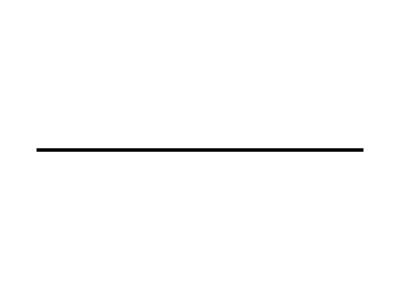
```mathematica
vizColors=RGBColor/@{"#2a78d6","#eb6834","#1baf7a","#eda100"};vizMuted=RGBColor["#898781"];vizStyle[title_String,xlabel_,ylabel_]:={Frame->True,Axes->False,Background->RGBColor["#fcfcfb"],ImageSize->760,AspectRatio->0.58,FrameStyle->Directive[RGBColor["#c3c2b7"],AbsoluteThickness[1]],FrameTicksStyle->Directive[RGBColor["#52514e"],FontFamily->"Arial",FontSize->12],GridLines->Automatic,GridLinesStyle->Directive[RGBColor["#e1e0d9"],AbsoluteThickness[0.6]],FrameLabel->{Style[xlabel,RGBColor["#52514e"],FontFamily->"Arial",13],Style[ylabel,RGBColor["#52514e"],FontFamily->"Arial",13]},PlotLabel->Style[title,RGBColor["#0b0b0b"],FontFamily->"Arial",14],LabelStyle->Directive[RGBColor["#0b0b0b"],FontFamily->"Arial",FontSize->12],ImagePadding->{{70,20},{55,35}}};dotLineLegend[labels_List,colors_List,kinds_List]:=Placed[SwatchLegend[colors,labels,LegendMarkers->(If[#1==="dot",-Graphics-,-Graphics-]&)/@kinds,LegendMarkerSize->16,LabelStyle->Directive[RGBColor["#0b0b0b"],FontFamily->"Arial",FontSize->12],LegendLayout->{"Row",2}],Below];exportFigure[name_String,graphic_]:=Module[{path=FileNameJoin[{figureDirectory,name}],bytes,out,i=9,n,type,stream},Quiet[Export[path,graphic,"PNG",ImageResolution->110],{ImportExport`RegisterFormat::interr}];bytes=Normal[ReadByteArray[path]];out=Take[bytes,8];While[i≤Length[bytes],n=FromDigits[bytes⟦i;;i+3⟧,256];type=FromCharacterCode[bytes⟦i+4;;i+7⟧];If[!(type==="tEXt"&&StringStartsQ[FromCharacterCode[bytes⟦i+8;;i+7+n⟧],"Creation Time"]),out=Join[out,bytes⟦i;;i+11+n⟧]];i+=12+n];stream=OpenWrite[path,BinaryFormat->True];BinaryWrite[stream,out];Close[stream];name];figureFiles={};sciLabel[x_]:=If[x==0,"0",Module[{e=Floor[Log10[Abs[x]]],mant},mant=Round[(100 Abs[x])/10^e];If[mant==1000,mant=100;e=e+1];If[x<0,"-",""]<>ToString[Quotient[mant,100]]<>"."<>IntegerString[Mod[mant,100],10,2]<>"e"<>ToString[e]]];{Length[vizColors],DirectoryQ[figureDirectory]}
```

```mathematica
Module[{mine=freeSpectrumResults[{1,3}]["mine"],t=freeTables[{1,3}],bands,dots,g},bands=Table[Select[Values[GroupBy[Select[mine,#1["parity"]==parity&],{#1["s"],#1["index"]}&,SortBy[({#1["k"],#1["eps"]}&)/@#1,First]&]],Length[#1]≥2&],{parity,{1,-1}}];dots=Table[Select[Transpose[{columnOf[t,"k"],columnOf[t,"eps"],columnOf[t,"parity"]}],#1⟦3⟧==parity&]⟦All,1;;2⟧,{parity,{1,-1}}];g=Legended[Show[ListLinePlot[Join[bands⟦1⟧,bands⟦2⟧],PlotStyle->Join[ConstantArray[Directive[vizColors⟦1⟧,AbsoluteThickness[1.2]],Length[bands⟦1⟧]],ConstantArray[Directive[vizColors⟦2⟧,AbsoluteThickness[1.2]],Length[bands⟦2⟧]]],PlotRange->{{-0.02,1.02},{-4.1,4.1}}],ListPlot[dots,PlotStyle->(Directive[#1,AbsolutePointSize[5]]&)/@vizColors⟦1;;2⟧],Sequence@@vizStyle["Free spectrum, m = H = 1, L = 3: levels of both block types vs |k| (Delta k = 0.25 m)","|k| / m","eps / m"]],dotLineLegend[{"brane parity +, Rust CVODE","brane parity +, NDSolve shooting","brane parity -, Rust CVODE","brane parity -, NDSolve shooting"},vizColors⟦{1,1,2,2}⟧,{"dot","line","dot","line"}]];AppendTo[figureFiles,exportFigure["free_spectrum_m1_L3.png",g]];g]
```

```mathematica
Module[{lengths=Range[8/5,22/5,1/20],plotMomentum,plusCurves,minusCurves,rustDots,g},plotMomentum[lv_,j_]:=Module[{a=N[((j-1/2) π)/lv],b=N[(j π)/lv],ga,c},ga=Sign[Sin[a lv]+a Cos[a lv]];Do[c=(a+b)/2;If[Sign[Sin[c lv]+c Cos[c lv]]==ga,a=c,b=c],{60}];(a+b)/2];plusCurves=Table[Table[{N[lv],N[√(1+((n π)/lv)^2)]},{lv,lengths}],{n,1,5}];minusCurves=Table[Table[{N[lv],√(1+plotMomentum[N[lv],j]^2)},{lv,lengths}],{j,1,5}];rustDots=Table[Flatten[Table[Module[{t=freeTables[{1,lv}]},Select[Transpose[{ConstantArray[N[lv],Length[t["rows"]]],columnOf[t,"eps"],columnOf[t,"n2"],columnOf[t,"parity"],columnOf[t,"s"]}],#1⟦3⟧==0&&#1⟦4⟧==parity&&#1⟦5⟧==1&&0.5≤#1⟦2⟧≤3.4&]⟦All,1;;2⟧],{lv,{2,3,4}}],1],{parity,{1,-1}}];g=Legended[Show[ListLinePlot[Join[plusCurves,minusCurves,{Table[{N[lv],0.},{lv,lengths}]}],PlotStyle->Join[ConstantArray[Directive[vizColors⟦1⟧,AbsoluteThickness[2]],5],ConstantArray[Directive[vizColors⟦2⟧,AbsoluteThickness[2]],5],{Directive[vizColors⟦3⟧,AbsoluteThickness[2]]}],PlotRange->{{1.55,4.45},{-0.15,3.45}}],ListPlot[{rustDots⟦1⟧,rustDots⟦2⟧,Table[{N[lv],0.},{lv,{2,3,4}}]},PlotStyle->(Directive[#1,AbsolutePointSize[9]]&)/@vizColors⟦1;;3⟧],Sequence@@vizStyle["k = 0, lambda = 0 box levels (m = 1): exact solution vs the Rust free spectra at L = 2, 3, 4","tip cutoff L (units 1/H)","eps / m"]],dotLineLegend[{"parity +, sqrt(m^2 + (n pi/L)^2), exact","parity +, Rust","parity -, tan(pL) = -p/m, exact","parity -, Rust","brane zero mode eps = 0, exact","zero mode, Rust"},vizColors⟦{1,1,2,2,3,3}⟧,{"line","dot","line","dot","line","dot"}]];AppendTo[figureFiles,exportFigure["box_levels_vs_L.png",g]];g]
```

```mathematica
Module[{fine=Subdivide[-scfLength,0.,600],rustY=columnOf[scfProfiles,"y"]⟦1;;-1;;6⟧,g},g=Legended[Show[ListLinePlot[{Transpose[{fine,scfPot⟦1⟧/@fine-scfMass}],Transpose[{fine,scfPot⟦2⟧/@fine}]},PlotStyle->(Directive[#1,AbsoluteThickness[2]]&)/@vizColors⟦1;;2⟧,PlotRange->All],ListPlot[{Transpose[{rustY,columnOf[scfProfiles,"M_eff"]⟦1;;-1;;6⟧-scfMass}],Transpose[{rustY,columnOf[scfProfiles,"v_x"]⟦1;;-1;;6⟧}]},PlotStyle->(Directive[#1,AbsolutePointSize[6]]&)/@vizColors⟦1;;2⟧],Sequence@@vizStyle["Kohn-Sham pseudo-potential of the N = 8, lambda_hat_2, T = 0 ground state (L = 3, m = H = 1)","hidden coordinate y (tip -L to brane 0)","potential / m"]],dotLineLegend[{"M_eff - m = (15/16) lambda S_p, Rust","M_eff - m, Wolfram Language loop","v_x = -(lambda/16) n_p, Rust","v_x, Wolfram Language loop"},vizColors⟦{1,1,2,2}⟧,{"dot","line","dot","line"}]];AppendTo[figureFiles,exportFigure["scf_pseudo_potential.png",g]];g]
```

```mathematica
Module[{logPositive,rustY=columnOf[scfProfiles,"y"],g},logPositive[pairs_]:=With[{floor=Max[pairs⟦All,2⟧]/10^10},({#1⟦1⟧,Log10[#1⟦2⟧]}&)/@Select[pairs,#1⟦2⟧>floor&]];g=Legended[Show[ListLinePlot[{logPositive[Transpose[{scfGrid,scfNp}]],logPositive[Transpose[{scfGrid,scfSp}]]},PlotStyle->(Directive[#1,AbsoluteThickness[2]]&)/@vizColors⟦1;;2⟧,PlotRange->All],ListPlot[{logPositive[Transpose[{rustY,columnOf[scfProfiles,"n_p"]}]⟦1;;-1;;6⟧],logPositive[Transpose[{rustY,columnOf[scfProfiles,"S_p"]}]⟦1;;-1;;6⟧]},PlotStyle->(Directive[#1,AbsolutePointSize[6]]&)/@vizColors⟦1;;2⟧],Sequence@@vizStyle["Proper densities, N = 8, lambda_hat_2 ground state (points below 1e-10 of max omitted)","hidden coordinate y (tip -L to brane 0)","log10 density (per unit proper volume)"]],dotLineLegend[{"number density n_p, Rust","n_p, Wolfram Language loop","scalar density S_p, Rust","S_p, Wolfram Language loop"},vizColors⟦{1,1,2,2}⟧,{"dot","line","dot","line"}]];AppendTo[figureFiles,exportFigure["scf_proper_densities.png",g]];g]
```

```mathematica
Module[{mine=({#1⟦1⟧,Log10[Max[#1⟦2⟧,#1⟦3⟧]]}&)/@scfResiduals,rust=Transpose[{columnOf[scfHistory,"iteration"],Log10[MapThread[Max,{columnOf[scfHistory,"residual_n"],columnOf[scfHistory,"residual_S"]}]]}],g},g=Legended[Show[ListLinePlot[{mine},PlotStyle->{Directive[vizColors⟦1⟧,AbsoluteThickness[2]]},PlotRange->All],ListPlot[{rust},PlotStyle->{Directive[vizColors⟦2⟧,AbsolutePointSize[8]]}],Plot[{-10.,-12.},{xPlot,0,Max[Length[mine],Length[rust]]},PlotStyle->(Directive[vizMuted,AbsoluteThickness[1.2],Dashing[{0.012,0.01}]]&)/@{1,2}],Sequence@@vizStyle["Self-consistency: Anderson mixing (beta 0.4, history 6) from zero densities","iteration","log10 max(|dn_c|, |dS_c|)/D"]],dotLineLegend[{"Rust CVODE loop (stops at 1e-10)","Wolfram Language loop (stops at 1e-12)","tolerances 1e-10 and 1e-12"},{vizColors⟦2⟧,vizColors⟦1⟧,vizMuted},{"dot","line","line"}]];AppendTo[figureFiles,exportFigure["scf_convergence.png",g]];g]
```

```mathematica
Module[{labels,values,g},labels={"k = 0 box: exact vs Rust","free spectra: NDSolve vs Rust ("<>ToString[Total[(#1["levels"]&)/@Values[freeSpectrumResults]]]<>" levels)","free spectra: scalar charges","closed-shell tables","SCF: eps_HOMO","SCF: E_0","SCF: n_c / D","SCF: M_eff(y)","SCF: v_x(y)","SCF: full spectrum ("<>ToString[scfSpectrumComparison["levels"]]<>" levels)","SCF: KS gap"};values={Max[(#1["maxAbsDeviation"]&)/@Values[boxComparison]],Max[(#1["maxAbsDeviation"]&)/@Values[freeSpectrumResults]],Max[(#1["maxScalarChargeDeviation"]&)/@Values[freeSpectrumResults]],Max[(#1["maxAbsDeviation"]&)/@Values[closedShellComparison]],scfComparison["epsHomoDeviation"],scfComparison["energyDeviation"],scfComparison["ncMaxDeviationOverD"],scfComparison["mEffMaxAbsDeviation"],scfComparison["vxMaxAbsDeviation"],scfSpectrumComparison["maxAbsDeviation"],scfSpectrumComparison["ksGapDeviation"]};g=BarChart[-Log10[values],ChartStyle->vizColors⟦1⟧,BarOrigin->Left,BarSpacing->0.35,ChartLabels->Placed[(Style[#1,RGBColor["#52514e"],FontFamily->"Arial",12]&)/@labels,Before],LabelingFunction->(Placed[Style["max dev "<>sciLabel[10^-#1],RGBColor["#0b0b0b"],FontFamily->"Arial",11],After]&),Frame->{{False,False},{True,False}},FrameStyle->Directive[RGBColor["#c3c2b7"],AbsoluteThickness[1]],FrameTicksStyle->Directive[RGBColor["#52514e"],FontFamily->"Arial",FontSize->12],FrameLabel->{{None,None},{Style["digits of agreement, -log10(max absolute deviation)",RGBColor["#52514e"],FontFamily->"Arial",13],None}},PlotLabel->Style["Agreement of the Mathematica computations with the Rust Kohn-Sham solver",RGBColor["#0b0b0b"],FontFamily->"Arial",14],GridLines->{Automatic,None},GridLinesStyle->Directive[RGBColor["#e1e0d9"],AbsoluteThickness[0.6]],Background->RGBColor["#fcfcfb"],ImageSize->760,AspectRatio->0.62,ImagePadding->{{250,30},{55,35}},PlotRange->{{0,16},All}];AppendTo[figureFiles,exportFigure["agreement_overview.png",g]];g]
```

## Report and fail-fast verification

Summary of the measured agreement (all computed above; deviations are absolute unless marked otherwise; Rust = the committed CVODE outputs under artifacts/dirac16complex/kohn-sham/rust/spectrum and rust/scf).

```mathematica
findingsRows={{"exact theory","checks of wolfram/Dirac16ComplexKohnSham.wl (all pass)",theoryCheckSummary["checkCount"]},{"k = 0 box","exact levels vs Rust, six files",Max[(#1["maxAbsDeviation"]&)/@Values[boxComparison]]},{"k = 0 box","NDSolve shooting vs exact levels",Max[(#1["k0VsExactBoxMaxAbsDeviation"]&)/@Values[freeSpectrumResults]]},{"zero mode","slope d eps/dk vs -s c (Richardson, h = 1e-4)",zeroModeSlopeDeviation},{"free spectra","levels compared (six files, keys identical)",Total[(#1["levels"]&)/@Values[freeSpectrumResults]]},{"free spectra","eps, NDSolve vs Rust",Max[(#1["maxAbsDeviation"]&)/@Values[freeSpectrumResults]]},{"free spectra","scalar / pressure charges vs Rust",{Max[(#1["maxScalarChargeDeviation"]&)/@Values[freeSpectrumResults]],Max[(#1["maxPressureChargeDeviation"]&)/@Values[freeSpectrumResults]]}},{"free spectra","linear-system matching residual (max)",Max[(#1["maxMatchingResidual"]&)/@Values[freeSpectrumResults]]},{"free spectra","worst level per file vs WorkingPrecision-32 reference: notebook / Rust",{Max[(Abs[#1["notebookMinusReference"]]&)/@Values[errorAttribution]],Max[(Abs[#1["rustMinusReference"]]&)/@Values[errorAttribution]]}},{"closed shells","tables m = 1, 3 (L = 3) vs Rust",Max[(#1["maxAbsDeviation"]&)/@Values[closedShellComparison]]},{"SCF N = 8","iterations to 1e-12 (Rust: to 1e-10)",{scfComparison["iterations"],scfComparison["rustIterations"]}},{"SCF N = 8","eps_HOMO (= mu), WL vs Rust",scfComparison["epsHomoDeviation"]},{"SCF N = 8","E_0, WL vs Rust",scfComparison["energyDeviation"]},{"SCF N = 8","sum eps / Hartree / exchange energies",{scfComparison["ksSumDeviation"],scfComparison["hartreeDeviation"],scfComparison["exchangeDeviation"]}},{"SCF N = 8","M_eff(y) and v_x(y) on the grid (max)",{scfComparison["mEffMaxAbsDeviation"],scfComparison["vxMaxAbsDeviation"]}},{"SCF N = 8","n_c and S_c relative to D",{scfComparison["ncMaxDeviationOverD"],scfComparison["scMaxDeviationOverD"]}},{"SCF N = 8","HOMO orbital (a, b) on the grid",scfComparison["homoProfileMaxDeviation"]},{"SCF N = 8","complete spectrum: levels, shells (keys identical)",{scfSpectrumComparison["levels"],scfSpectrumComparison["shellsUsed"]}},{"SCF N = 8","complete spectrum: eps, WL vs Rust",scfSpectrumComparison["maxAbsDeviation"]},{"SCF N = 8","KS gap / LUMO / sea top",{scfSpectrumComparison["ksGapDeviation"],scfSpectrumComparison["epsLumoDeviation"],scfSpectrumComparison["seaTopDeviation"]}}};Grid[Prepend[({#1⟦1⟧,#1⟦2⟧,StringRiffle[(If[IntegerQ[#1],ToString[#1],sciLabel[#1]]&)/@Flatten[{#1⟦3⟧}]," / "]}&)/@findingsRows,{"part","quantity","value"}],Frame->All,Alignment->Left]
```

The facts quoted in the text cells are checked against the committed files, so that the prose cannot drift from the outputs: the free-spectrum window and shells, the closed-shell limit 1300, and the parameter set of the self-consistent comparison.

```mathematica
textParameterChecks=Association["freeSpectraWindowFourMAndShellsUpTo16"->AllTrue[freeConfigurations,Module[{t=freeTables[#1]},Max[Abs[columnOf[t,"eps"]]]<4 #1⟦1⟧&&Sort[DeleteDuplicates[Round[columnOf[t,"n2"]]]]===representableShells[16]&&AllTrue[columnOf[t,"weight"],#1==0&]]&],"closedShellTablesStopAbove1300"->AllTrue[{1,3},Module[{tab=rustClosedShells[#1]},tab⟦-1,1⟧>1300&&tab⟦-2,1⟧≤1300]&],"scfParameterSetAsStated"->scfSetupChecks["runParametersAsStated"]&&scfSetupChecks["runIsLambdaHat2OfN8"]&&scfRun["parameters"]["mixBeta"]==0.4&&scfRun["parameters"]["mixHistory"]==6&&scfRun["parameters"]["tol"]==1/10^10];textParameterChecks
```

All checks are collected in notebookChecks; the report artifacts/dirac16complex/kohn-sham/mathematica-report.json records every check, the measurements printed by the verifier, the full comparison records and the SHA-256 of every input file read (numbers only, no timings and no absolute paths, so a repeated run on the same machine gives the same file; engine.binary is the platform-specific binary name).

```mathematica
notebookChecks=Join[Association["theory_packageChecksAllPass"->theoryCheckSummary["checkCount"]>0&&theoryCheckSummary["failed"]==={}],KeyMap["geometry_"<>#1&,geometryChecks],KeyMap["reduction_"<>#1&,reductionChecks],KeyMap["blocks_"<>#1&,blockChecks],KeyMap["realForm_"<>#1&,realFormChecks],KeyMap["pruefer_"<>#1&,pruferChecks],KeyMap["box_"<>#1&,boxChecks],KeyMap["splitting_"<>#1&,splittingChecks],KeyMap["shooting_"<>#1&,shootingChecks],KeyMap["scf_"<>#1&,scfChecks],KeyMap["engine_"<>#1&,engineChecks],KeyMap["text_"<>#1&,textParameterChecks],Association["figuresExported"->Length[figureFiles]==6&&AllTrue[figureFiles,FileExistsQ[FileNameJoin[{figureDirectory,#1}]]&]]];notebookChecks=TrueQ/@notebookChecks;jsonReady[a_Association]:=jsonReady/@a;jsonReady[l_List]:=jsonReady/@l;jsonReady[x_Real]:=With[{y=N[x]},If[Abs[y]<1/10^300,0.,y]];jsonReady[x_Rational]:=N[x];jsonReady[x_Integer]:=x;jsonReady[x_String]:=x;jsonReady[True]:=True;jsonReady[False]:=False;jsonReady[Null]:=Null;jsonReady[_Missing]:=Null;jsonReady[_DirectedInfinity]:=Null;jsonReady[x_]:=ToString[x,InputForm];reportMeasurements=Association["theoryPackageCheckCount"->theoryCheckSummary["checkCount"],"zeroModeSplittingC_m1_H1_L3"->N[cSplittingM1L3],"zeroModeSlopeMaxDeviation"->zeroModeSlopeDeviation,"boxExactLevelCount"->Total[(#1["levels"]&)/@Values[boxComparison]],"boxExactVsRustMaxAbsDeviation"->Max[(#1["maxAbsDeviation"]&)/@Values[boxComparison]],"boxNDSolveVsExactMaxAbsDeviation"->Max[(#1["k0VsExactBoxMaxAbsDeviation"]&)/@Values[freeSpectrumResults]],"freeSpectraLevelCount"->Total[(#1["levels"]&)/@Values[freeSpectrumResults]],"freeSpectraMaxAbsDeviation"->Max[(#1["maxAbsDeviation"]&)/@Values[freeSpectrumResults]],"freeSpectraMaxScalarChargeDeviation"->Max[(#1["maxScalarChargeDeviation"]&)/@Values[freeSpectrumResults]],"freeSpectraMaxPressureChargeDeviation"->Max[(#1["maxPressureChargeDeviation"]&)/@Values[freeSpectrumResults]],"freeSpectraMaxPressureChargeRelativeDeviation"->Max[(#1["maxPressureChargeRelativeDeviation"]&)/@Values[freeSpectrumResults]],"freeSpectraMaxMatchingResidual"->Max[(#1["maxMatchingResidual"]&)/@Values[freeSpectrumResults]],"worstLevelNotebookMinusReferenceMax"->Max[(Abs[#1["notebookMinusReference"]]&)/@Values[errorAttribution]],"worstLevelRustMinusReferenceMax"->Max[(Abs[#1["rustMinusReference"]]&)/@Values[errorAttribution]],"closedShellEntries_m1_L3"->closedShellComparison[1]["entries"],"closedShellEntries_m3_L3"->closedShellComparison[3]["entries"],"closedShellsMaxAbsDeviation"->Max[(#1["maxAbsDeviation"]&)/@Values[closedShellComparison]],"scfLambdaHat"->scfLambdaHat,"scfIterations"->scfComparison["iterations"],"scfFinalResidual"->Max[scfComparison["finalResidualN"],scfComparison["finalResidualS"]],"scfEpsHomo"->scfComparison["epsHomo"],"scfEpsHomoDeviation"->scfComparison["epsHomoDeviation"],"scfEnergy"->scfComparison["energy"],"scfEnergyDeviation"->scfComparison["energyDeviation"],"scfEnergyRelativeDeviation"->scfComparison["energyDeviation"]/Abs[scfComparison["rustEnergy"]],"scfKsSumDeviation"->scfComparison["ksSumDeviation"],"scfHartreeDeviation"->scfComparison["hartreeDeviation"],"scfExchangeDeviation"->scfComparison["exchangeDeviation"],"scfMeffMaxAbsDeviation"->scfComparison["mEffMaxAbsDeviation"],"scfMeffTolerance"->scfComparison["mEffTolerance"],"scfVxMaxAbsDeviation"->scfComparison["vxMaxAbsDeviation"],"scfVxTolerance"->scfComparison["vxTolerance"],"scfNcMaxDeviationOverD"->scfComparison["ncMaxDeviationOverD"],"scfScMaxDeviationOverD"->scfComparison["scMaxDeviationOverD"],"scfHomoProfileMaxDeviation"->scfComparison["homoProfileMaxDeviation"],"scfSpectrumLevelCount"->scfSpectrumComparison["levels"],"scfSpectrumShells"->scfSpectrumComparison["shellsUsed"],"scfSpectrumMaxAbsDeviation"->scfSpectrumComparison["maxAbsDeviation"],"scfEpsFreeMaxAbsDeviation"->scfSpectrumComparison["epsFreeMaxAbsDeviation"],"scfKsGap"->scfSpectrumComparison["ksGap"],"scfKsGapDeviation"->scfSpectrumComparison["ksGapDeviation"],"scfEpsLumoDeviation"->scfSpectrumComparison["epsLumoDeviation"],"scfSeaTopDeviation"->scfSpectrumComparison["seaTopDeviation"]];reportSources=SortBy[({relativePath[#1],ToLowerCase[FileHash[#1,"SHA256",All,"HexString"]]}&)/@sourceFiles,First];mathematicaReport=jsonReady[Association["schemaVersion"->1,"producer"->"notebooks/Dirac16ComplexKohnSham.nb (built by scripts/build_dirac16complex_ks_mathematica_notebook.wls, evaluated headless by scripts/verify_dirac16complex_ks_mathematica_notebook.wls)","provenance"->"New notebook (none of the three rustSolveIt repositories contains a Mathematica notebook, recorded in Stage 3); modelled on the Stage-3 notebook notebooks/Dirac16ComplexDarkSector.nb and its builder/verifier.","wolframVersion"->$VersionNumber,"fixtureSha256"->fixtureHash,"inputs"->reportSources⟦All,1⟧,"method"->Association["symbolic"->"geometry, reduced Dirac equation, exact block diagonalisation, real two-component form and Pruefer form derived with Dirac16ComplexGeometry / Dirac16ComplexKohnSham and compared exactly with the Rust constants (generated.rs) and the printed equations of print-config","box"->"exact k = 0, lambda = 0 solution; parity - roots by exact-arithmetic bisection to 30 digits","shooting"->"NDSolve (ParametricNDSolveValue) Pruefer shooting in u = y + L with the variational equation; oscillation count over the window; bracketed Newton roots; linear-system matching residuals and charges","scf"->"Wolfram Language Kohn-Sham loop on the discrete problem of the Rust code (301-point grid, natural cubic spline, Simpson rule), Anderson mixing, tolerance 1e-12; complete spectrum of the final potential compared key by key"],"theoryPackage"->theoryCheckSummary,"symbolic"->Association["geometry"->geometryChecks,"reduction"->reductionChecks,"blocks"->blockChecks,"realForm"->realFormChecks,"pruefer"->pruferChecks,"box"->boxChecks,"splitting"->splittingChecks,"zeroModeSplittingClosedForm"->ToString[cSplitting,InputForm]],"measuredFacts"->Association["rustBlockLabels"->If[TrueQ[realFormChecks["rustLabelSIsMinusJEigenvalue"]],"on every Rust block (generated.rs BLOCK_BASIS) the eigenvalue of J = gamma^0 gamma^1 gamma^4 is -s, i.e. the label s is the eigenvalue of -J = gamma^1 gamma^0 gamma^4; the comment in generated.rs reads J = s. Both block types enter every sum with the same multiplicity, so no result depends on the label convention.","not established"],"rustChargeColumns"->"scalar_charge and pressure_charge of the Rust level files are the charges of the state of block type s: Integral(-2 s a b) and Integral(-s kappa k (a^2 - b^2)) of the normalised profile","homoProfileBlockType"->scfComparison["homoProfileBlockType"]],"shooting"->shootingResult,"scf"->scfResult,"engine"->Association["binary"->"studies/dirac16complex_kohn_sham/target/release/"<>FileNameTake[binaryPath],"command"->"print-config","exitCode"->printConfig["ExitCode"],"lastLine"->If[printConfigLines==={},"",Last[printConfigLines]],"checks"->engineChecks],"textParameters"->textParameterChecks,"figures"->("artifacts/dirac16complex/kohn-sham/figures/mathematica/"<>#1&)/@figureFiles,"measurements"->reportMeasurements,"checks"->notebookChecks,"checkCount"->Length[notebookChecks],"failedChecks"->Keys[Select[notebookChecks,!#1&]],"verdict"->If[And@@Values[notebookChecks],"SUCCESS","FAILURE"],"sourceSha256"->Association[Rule@@@reportSources]]];reportText=StringReplace[ExportString[mathematicaReport,"RawJSON","Compact"->False],{"\r\n"->"\n","\\/"->"/"}]<>"\n";reportStream=OpenWrite[reportPath,BinaryFormat->True];BinaryWrite[reportStream,ToCharacterCode[reportText,"UTF-8"]];Close[reportStream];{Length[notebookChecks],mathematicaReport["verdict"],FileByteCount[reportPath]}
```

```mathematica
If[!And@@Values[notebookChecks],Failure["NotebookVerification",Association["FailedChecks"->Keys[Select[notebookChecks,!#1&]]]],notebookChecks]
```